### Not used

#### Define Generalized Riemann Problem System of PDES

```mathematica
f[z_]:=1 - z^4/zh^4
X = {r[t,σ],z[t,σ],u[t,σ],v[t,σ],w[t,σ],q[t,σ]};
(*A = {{1,0,0,0,0,0},
{0,1,0,0,0,0},
{0,0,0,1,0,0},
{0,0,(l^4 r[t,σ]^4)/z[t,σ]^8 f[z[t,σ]]^2,0,0,0},
{0,0,0,0,0,1},
{0,0,0,0,(l^4 r[t,σ]^4)/z[t,σ]^8 f[z[t,σ]]^2,0}};*)
A = {{1,0,0,0,0,0},
{0,1,0,0,0,0},
{0,0,0,1,0,0},
{0,0,(l^4 X[[1]]^4)/X[[2]]^8 f[X[[2]]]^2,0,0,0},
{0,0,0,0,0,1},
{0,0,0,0,(l^4 X[[1]]^4)/X[[2]]^8 f[X[[2]]]^2,0}};
Y={X[[4]]-X[[3]],X[[6]]-X[[5]],0,HoldForm[F[X]],0,HoldForm[G[X]]}
D[X,t] - A.D[X,σ]-Y//MatrixForm
```

{-u[t,σ]+v[t,σ],q[t,σ]-w[t,σ],0,F[X],0,G[X]}

(u[t,σ]-v[t,σ]-r^(0,1)[t,σ]+r^(1,0)[t,σ]
-q[t,σ]+w[t,σ]-z^(0,1)[t,σ]+z^(1,0)[t,σ]
-v^(0,1)[t,σ]+u^(1,0)[t,σ]
-F[X]-(l^4 r[t,σ]^4 (1-z[t,σ]^4/zh^4)^2 u^(0,1)[t,σ])/z[t,σ]^8+v^(1,0)[t,σ]
-q^(0,1)[t,σ]+w^(1,0)[t,σ]
-G[X]-(l^4 r[t,σ]^4 (1-z[t,σ]^4/zh^4)^2 w^(0,1)[t,σ])/z[t,σ]^8+q^(1,0)[t,σ])

```mathematica
Eigs=Eigensystem[A]
```

{{1,1,-(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4))/(zh^4 z[t,σ]^4),-(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4))/(zh^4 z[t,σ]^4),(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4))/(zh^4 z[t,σ]^4),(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4))/(zh^4 z[t,σ]^4)},{{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,-(zh^4 z[t,σ]^4)/(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4)),1},{0,0,-(zh^4 z[t,σ]^4)/(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4)),1,0,0},{0,0,0,0,(zh^4 z[t,σ]^4)/(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4)),1},{0,0,(zh^4 z[t,σ]^4)/(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4)),1,0,0}}}

So each eigenvalue is 2-fold degenerate, and the eigenvectors are linearly independent, ie. A is diagonalizable

I think there may be this degeneracy because the r and z equations are each identical.

```mathematica
Eigs[[1]]
```

{1,1,-(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4))/(zh^4 z[t,σ]^4),-(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4))/(zh^4 z[t,σ]^4),(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4))/(zh^4 z[t,σ]^4),(l^2 r[t,σ]^2 (zh^4-z[t,σ]^4))/(zh^4 z[t,σ]^4)}

```mathematica
Table[Table[D[Eigs[[1]][[j]],X[[i]]],{i,Length[X]}].Eigs[[2]][[j]],{j,Length[X]}]
```

{0,0,0,0,0,0}

#### Choose better variables - 2+1D warped, hyperbolic and homogeneous

```mathematica
f[z_]:=1 - z^4/zh^4
g = (r^2 l^2)/z^4{{1,0},{0,1/f[z]}}
g00= -(r^2 l^2)/z^4 f[z]
```

{{(l^2 r^2)/z^4,0},{0,(l^2 r^2)/(z^4 (1-z^4/zh^4))}}

-(l^2 r^2 (1-z^4/zh^4))/z^4

```mathematica
X = {r,z};
Xd = {rd,zd};
Xp = {rp,zp};
Xrepl = {r->r[t,σ],rd->rd[t,σ],rp->rp[t,σ],z->z[t,σ],zd->zd[t,σ],zp->zp[t,σ]};
```

```mathematica
Table[D[gspat g00,X[[i]]],{i,2}]
Sum[D[gspat/g00,X[[k]]] Xd[[k]],{k,2}]/.Xrepl
```

{{{-(4 l^4 r^3 (1-z^4/zh^4))/z^8,0},{0,-(4 l^4 r^3)/z^8}},{{(8 l^4 r^4 (1-z^4/zh^4))/z^9+(4 l^4 r^4)/(z^5 zh^4),0},{0,(8 l^4 r^4)/z^9}}}

{{-(4 z[t,σ]^3 z^(1,0)[t,σ])/(zh^4 (1-z[t,σ]^4/zh^4)^2),0},{0,-(8 z[t,σ]^3 z^(1,0)[t,σ])/(zh^4 (1-z[t,σ]^4/zh^4)^3)}}

First thing to do is just write out the equations. Then we can collect them into matrices

```mathematica
Table[Sum[Sum[
D[g[[i,j]]/g00,X[[k]]] Xd[[k]]D[X[[j]]/.Xrepl,t] + g[[i,j]]/g00 D[Xd[[j]]/.Xrepl,t]
-D[g[[i,j]]/g00,X[[k]]]  Xp[[k]] D[X[[j]]/.Xrepl,σ] - g[[i,j]] g00 D[Xp[[j]]/.Xrepl,σ] + D[g[[j,k]]/g00,X[[i]]]Xp[[k]] D[X[[j]]/.Xrepl,σ]
,{k,2}],{j,2}],{i,2}]
```

{(4 z^3 zp r^(0,1)[t,σ])/((1-z^4/zh^4)^2 zh^4)+(2 l^4 r^4 (1-z^4/zh^4) rp^(0,1)[t,σ])/z^8-(4 z^3 zd r^(1,0)[t,σ])/((1-z^4/zh^4)^2 zh^4)-(2 rd^(1,0)[t,σ])/(1-z^4/zh^4),-(4 rp z^3 r^(0,1)[t,σ])/((1-z^4/zh^4)^2 zh^4)+(2 l^4 r^4 zp^(0,1)[t,σ])/z^8-(8 z^3 zd z^(1,0)[t,σ])/((1-z^4/zh^4)^3 zh^4)-(2 zd^(1,0)[t,σ])/((1-z^4/zh^4)^2)}

```mathematica
Xtot = {r,z,rd,zd,rp,zp};
Cmat = {{-(4 z^3 zd)/((1-z^4/zh^4)^2 zh^4),0,-2/(1-z^4/zh^4),0,0,0},
{0,-(8 z^3 zd)/((1-z^4/zh^4)^3 zh^4),0,-2/((1-z^4/zh^4)^2),0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}};
MatrixForm[%]
Bmat =  {{(4 z^3 zp)/((1-z^4/zh^4)^2 zh^4),0,0,0,(2 l^4 r^4 (1-z^4/zh^4))/z^8,0},
{-(4 rp z^3)/((1-z^4/zh^4)^2 zh^4),0,0,0,0,(2 l^4 r^4)/z^8},
{0,0,0,0,0,0},
{0,0,0,0,0,0},
{0,0,-1,0,0,0},
{0,0,0,-1,0,0}};
MatrixForm[%]

Cmat.D[Xtot/.Xrepl,t] + Bmat.D[Xtot/.Xrepl,σ]
```

(-(4 z^3 zd)/((1-z^4/zh^4)^2 zh^4) | 0 | -2/(1-z^4/zh^4) | 0 | 0 | 0
0 | -(8 z^3 zd)/((1-z^4/zh^4)^3 zh^4) | 0 | -2/((1-z^4/zh^4)^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

((4 z^3 zp)/((1-z^4/zh^4)^2 zh^4) | 0 | 0 | 0 | (2 l^4 r^4 (1-z^4/zh^4))/z^8 | 0
-(4 rp z^3)/((1-z^4/zh^4)^2 zh^4) | 0 | 0 | 0 | 0 | (2 l^4 r^4)/z^8
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0)

{(4 z^3 zp r^(0,1)[t,σ])/((1-z^4/zh^4)^2 zh^4)+(2 l^4 r^4 (1-z^4/zh^4) rp^(0,1)[t,σ])/z^8-(4 z^3 zd r^(1,0)[t,σ])/((1-z^4/zh^4)^2 zh^4)-(2 rd^(1,0)[t,σ])/(1-z^4/zh^4),-(4 rp z^3 r^(0,1)[t,σ])/((1-z^4/zh^4)^2 zh^4)+(2 l^4 r^4 zp^(0,1)[t,σ])/z^8-(8 z^3 zd z^(1,0)[t,σ])/((1-z^4/zh^4)^3 zh^4)-(2 zd^(1,0)[t,σ])/((1-z^4/zh^4)^2),0,0,-rd^(0,1)[t,σ]+rp^(1,0)[t,σ],-zd^(0,1)[t,σ]+zp^(1,0)[t,σ]}

Now add in the last two auxiliary conditions

We need time derivatives so we can fill the two rows for rd and zd

```mathematica
D[Sum[z^4/(l^2 r^2)g[[i,j]]Xd[[i]] Xp[[j]],{i,2},{j,2}]/.Xrepl,t]
```

rp[t,σ] rd^(1,0)[t,σ]+rd[t,σ] rp^(1,0)[t,σ]+(4 z[t,σ]^3 zd[t,σ] zp[t,σ] z^(1,0)[t,σ])/(zh^4 (1-z[t,σ]^4/zh^4)^2)+(zp[t,σ] zd^(1,0)[t,σ])/(1-z[t,σ]^4/zh^4)+(zd[t,σ] zp^(1,0)[t,σ])/(1-z[t,σ]^4/zh^4)

```mathematica
D[Sum[z^4/(l^2 r^2)g[[i,j]]Xd[[i]] Xp[[j]],{i,2},{j,2}]/.Xrepl,σ]
```

rp[t,σ] rd^(0,1)[t,σ]+rd[t,σ] rp^(0,1)[t,σ]+(4 z[t,σ]^3 zd[t,σ] zp[t,σ] z^(0,1)[t,σ])/(zh^4 (1-z[t,σ]^4/zh^4)^2)+(zp[t,σ] zd^(0,1)[t,σ])/(1-z[t,σ]^4/zh^4)+(zd[t,σ] zp^(0,1)[t,σ])/(1-z[t,σ]^4/zh^4)

```mathematica
(*D[(Sum[z^4/(l^2 r^2)g[[i,j]](Xp[[i]] Xp[[j]]+Xd[[i]] Xd[[j]]),{i,2},{j,2}])/.Xrepl,t]
D[(-(l^2 r^2)/z^4)/.Xrepl,t]*)
```

```mathematica
Xtot = {r,z,rd,zd,rp,zp};
Cmat = {{-(4 z^3 zd)/((1-z^4/zh^4)^2 zh^4),0,-2/(1-z^4/zh^4),0,0,0},
{0,-(8 z^3 zd)/((1-z^4/zh^4)^3 zh^4),0,-2/((1-z^4/zh^4)^2),0,0},
{0,0,rp,zp/(1-z^4/zh^4),rd,0},
{0,0,0,(4 z^3 zp^2)/(zh^4 (1-z^4/zh^4)^2),0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}};
MatrixForm[%]
Bmat =  {{(4 z^3 zp)/((1-z^4/zh^4)^2 zh^4),0,0,0,(2 l^4 r^4 (1-z^4/zh^4))/z^8,0},
{-(4 rp z^3)/((1-z^4/zh^4)^2 zh^4),0,0,0,0,(2 l^4 r^4)/z^8},
{0,(4 z^3 zd^2)/(zh^4 (1-z^4/zh^4)^2),0,0,0,0},
{0,0,rp,zp/(1-z^4/zh^4),rd,zd/(1-z^4/zh^4)},
{0,0,-1,0,0,0},
{0,0,0,-1,0,0}};
MatrixForm[%]

Cmat.D[Xtot/.Xrepl,t] + Bmat.D[Xtot/.Xrepl,σ]
```

(-(4 z^3 zd)/((1-z^4/zh^4)^2 zh^4) | 0 | -2/(1-z^4/zh^4) | 0 | 0 | 0
0 | -(8 z^3 zd)/((1-z^4/zh^4)^3 zh^4) | 0 | -2/((1-z^4/zh^4)^2) | 0 | 0
0 | 0 | rp | zp/(1-z^4/zh^4) | rd | 0
0 | 0 | 0 | (4 z^3 zp^2)/((1-z^4/zh^4)^2 zh^4) | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

((4 z^3 zp)/((1-z^4/zh^4)^2 zh^4) | 0 | 0 | 0 | (2 l^4 r^4 (1-z^4/zh^4))/z^8 | 0
-(4 rp z^3)/((1-z^4/zh^4)^2 zh^4) | 0 | 0 | 0 | 0 | (2 l^4 r^4)/z^8
0 | (4 z^3 zd^2)/((1-z^4/zh^4)^2 zh^4) | 0 | 0 | 0 | 0
0 | 0 | rp | zp/(1-z^4/zh^4) | rd | zd/(1-z^4/zh^4)
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0)

{(4 z^3 zp r^(0,1)[t,σ])/((1-z^4/zh^4)^2 zh^4)+(2 l^4 r^4 (1-z^4/zh^4) rp^(0,1)[t,σ])/z^8-(4 z^3 zd r^(1,0)[t,σ])/((1-z^4/zh^4)^2 zh^4)-(2 rd^(1,0)[t,σ])/(1-z^4/zh^4),-(4 rp z^3 r^(0,1)[t,σ])/((1-z^4/zh^4)^2 zh^4)+(2 l^4 r^4 zp^(0,1)[t,σ])/z^8-(8 z^3 zd z^(1,0)[t,σ])/((1-z^4/zh^4)^3 zh^4)-(2 zd^(1,0)[t,σ])/((1-z^4/zh^4)^2),(4 z^3 zd^2 z^(0,1)[t,σ])/((1-z^4/zh^4)^2 zh^4)+rp rd^(1,0)[t,σ]+rd rp^(1,0)[t,σ]+(zp zd^(1,0)[t,σ])/(1-z^4/zh^4),rp rd^(0,1)[t,σ]+rd rp^(0,1)[t,σ]+(zp zd^(0,1)[t,σ])/(1-z^4/zh^4)+(zd zp^(0,1)[t,σ])/(1-z^4/zh^4)+(4 z^3 zp^2 zd^(1,0)[t,σ])/((1-z^4/zh^4)^2 zh^4),-rd^(0,1)[t,σ]+rp^(1,0)[t,σ],-zd^(0,1)[t,σ]+zp^(1,0)[t,σ]}

To be invertible and hyperbolic we need both matrices to be non degenerate

```mathematica
Simplify[Det[Cmat]]
```

-(128 rp z^9 zd^2 zh^16 zp^2)/((z^4-zh^4)^7)

```mathematica
Simplify[Det[Bmat]]
```

-(32 l^4 r^4 zd^2 zh^8 (rp zd-rd zp))/(z^2 (z^4-zh^4)^4)

```mathematica
Inverse[Cmat].Bmat;
MatrixForm[%]
Eigensystem[%%]
```

(-zp/zd | -(2 zd)/(rp (1-z^4/zh^4)) | -(rd (1-z^4/zh^4) zh^4)/(2 rp z^3 zd)+((1-z^4/zh^4)^2 zh^8)/(8 z^6 zd zp) | ((1-z^4/zh^4) zh^8)/(8 rp z^6 zd) | -(l^4 r^4 (1-z^4/zh^4)^3 zh^4)/(2 z^11 zd)+(rd (1-z^4/zh^4)^2 zh^8)/(8 rp z^6 zd zp) | ((1-z^4/zh^4) zh^8)/(8 rp z^6 zp)
(rp (1-z^4/zh^4))/(2 zd) | 0 | -(rp (1-z^4/zh^4)^3 zh^8)/(16 z^6 zd zp^2) | -((1-z^4/zh^4)^2 zh^8)/(16 z^6 zd zp) | -(rd (1-z^4/zh^4)^3 zh^8)/(16 z^6 zd zp^2) | -(l^4 r^4 (1-z^4/zh^4)^3 zh^4)/(4 z^11 zd)-((1-z^4/zh^4)^2 zh^8)/(16 z^6 zp^2)
0 | (4 z^3 zd^2)/(rp (1-z^4/zh^4)^2 zh^4) | rd/rp-((1-z^4/zh^4) zh^4)/(4 z^3 zp) | -zh^4/(4 rp z^3) | -(rd (1-z^4/zh^4) zh^4)/(4 rp z^3 zp) | -(zd zh^4)/(4 rp z^3 zp)
0 | 0 | (rp (1-z^4/zh^4)^2 zh^4)/(4 z^3 zp^2) | ((1-z^4/zh^4) zh^4)/(4 z^3 zp) | (rd (1-z^4/zh^4)^2 zh^4)/(4 z^3 zp^2) | (zd (1-z^4/zh^4) zh^4)/(4 z^3 zp^2)
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0)

This is not  a useful approach, this will not lead to anything useful. 

I think it is better to go back to the simpler equations which were explicitly inhomogeneous

#### Coordinates for canonical kinetic term

```mathematica
f[z_]:=1 - z^4/zh^4
g = (r^2 l^2)/z^2{{-f[z],0,0},{0,1/f[z],0},{0,0,1}};
g00 = g[[1,1]]
MatrixForm[g]
```

(l^2 r^2 (-1+z^4/zh^4))/z^2

((l^2 r^2 (-1+z^4/zh^4))/z^2 | 0 | 0
0 | (l^2 r^2)/(z^2 (1-z^4/zh^4)) | 0
0 | 0 | (l^2 r^2)/z^2)

now want coordinates such that the kinetic term is canonical 

So we can do this using diff invariance

```mathematica
Clear[dρ]
g00^-1 dρ == g[[3,3]] dr
Simplify[%]
```

(dρ z^2)/(l^2 r^2 (-1+z^4/zh^4))==(dr l^2 r^2)/z^2

(dr l^3 r^3)/z==(dρ z^3 zh^4)/(l r z^4-l r zh^4)

```mathematica
ρ = Integrate[g00 g[[3,3]],{r,r0,roft}]
ζ = Integrate[g00 g[[3,3]],{r,r0,roft}]
```

(l^4 (-r0^5/5+roft^5/5) (-1+z^4/zh^4))/z^4

```mathematica
L = T0 g00
```

#### action for σ=r

```mathematica
Clear[zh]
f[z_]:=1-z^4/zh^4
met5DPL = l^2/z^2{{-HoldForm[f[z]],0,0,0,0},{0,HoldForm[1/f[z]],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
X = {t,z[r,t],r,θ,ϕ};
x= {t,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}];
Transpose[JXx].(met5DPL/.z->z[r,t]).JXx  //MatrixForm 
Simplify[-Det[%] z[r,t]^8/(l^8 r^4 Sin[θ]^2)]
```

(-(l^2 f[z])/z^2 | 0 | 0 | 0 | 0
0 | (l^2 1/f[z])/z^2 | 0 | 0 | 0
0 | 0 | l^2/z^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(-(l^2 f[z[r,t]])/z[r,t]^2+(l^2 1/f[z[r,t]] (z^(0,1)[r,t])^2)/z[r,t]^2 | (l^2 1/f[z[r,t]] z^(0,1)[r,t] z^(1,0)[r,t])/z[r,t]^2 | 0 | 0
(l^2 1/f[z[r,t]] z^(0,1)[r,t] z^(1,0)[r,t])/z[r,t]^2 | l^2/z[r,t]^2+(l^2 1/f[z[r,t]] (z^(1,0)[r,t])^2)/z[r,t]^2 | 0 | 0
0 | 0 | (l^2 r^2)/z[r,t]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,t]^2)

-1/f[z[r,t]] (z^(0,1)[r,t])^2+f[z[r,t]] (1+1/f[z[r,t]] (z^(1,0)[r,t])^2)

#### test new parametrization

```mathematica
repl = {r->r[τ,σ],z->z[τ,σ]}
```

{r→r[τ,σ],z→z[τ,σ]}

```mathematica
D[(r^2/z^4/.repl)D[(r/.repl),τ],σ]
D[(r^2/z^4/.repl)D[(r/.repl),σ],τ]
%-%%
```

(2 r[τ,σ] r^(0,1)[τ,σ] r^(1,0)[τ,σ])/z[τ,σ]^4-(4 r[τ,σ]^2 z^(0,1)[τ,σ] r^(1,0)[τ,σ])/z[τ,σ]^5+(r[τ,σ]^2 r^(1,1)[τ,σ])/z[τ,σ]^4

(2 r[τ,σ] r^(0,1)[τ,σ] r^(1,0)[τ,σ])/z[τ,σ]^4-(4 r[τ,σ]^2 r^(0,1)[τ,σ] z^(1,0)[τ,σ])/z[τ,σ]^5+(r[τ,σ]^2 r^(1,1)[τ,σ])/z[τ,σ]^4

(4 r[τ,σ]^2 z^(0,1)[τ,σ] r^(1,0)[τ,σ])/z[τ,σ]^5-(4 r[τ,σ]^2 r^(0,1)[τ,σ] z^(1,0)[τ,σ])/z[τ,σ]^5

```mathematica
D[(r^2/z^4 f[z]^-1/.repl)D[(z/.repl),τ],σ]
D[(r^2/z^4 f[z]^-1/.repl)D[(z/.repl),σ],τ]
%-%%
```

(2 r[τ,σ] r^(0,1)[τ,σ] z^(1,0)[τ,σ])/(f[z[τ,σ]] z[τ,σ]^4)-(4 r[τ,σ]^2 z^(0,1)[τ,σ] z^(1,0)[τ,σ])/(f[z[τ,σ]] z[τ,σ]^5)-(r[τ,σ]^2 f'[z[τ,σ]] z^(0,1)[τ,σ] z^(1,0)[τ,σ])/(f[z[τ,σ]]^2 z[τ,σ]^4)+(r[τ,σ]^2 z^(1,1)[τ,σ])/(f[z[τ,σ]] z[τ,σ]^4)

(2 r[τ,σ] z^(0,1)[τ,σ] r^(1,0)[τ,σ])/(f[z[τ,σ]] z[τ,σ]^4)-(4 r[τ,σ]^2 z^(0,1)[τ,σ] z^(1,0)[τ,σ])/(f[z[τ,σ]] z[τ,σ]^5)-(r[τ,σ]^2 f'[z[τ,σ]] z^(0,1)[τ,σ] z^(1,0)[τ,σ])/(f[z[τ,σ]]^2 z[τ,σ]^4)+(r[τ,σ]^2 z^(1,1)[τ,σ])/(f[z[τ,σ]] z[τ,σ]^4)

(2 r[τ,σ] z^(0,1)[τ,σ] r^(1,0)[τ,σ])/(f[z[τ,σ]] z[τ,σ]^4)-(2 r[τ,σ] r^(0,1)[τ,σ] z^(1,0)[τ,σ])/(f[z[τ,σ]] z[τ,σ]^4)

This is fine, we can use this knowing what the difference is, to find the solution. The lhs will still be in good the right form for us to use ie. linear and first order etc.

#### reparamterize 5D metric in terms of τ and σ

```mathematica
f[z_]:=1-z^4/zh^4
met5D = l^2/z^2{{-HoldForm[f[z]],0,0,0,0},{0,HoldForm[1/f[z]],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
```

```mathematica
X = {t[τ],z[σ,τ],r[σ,τ],θ,ϕ};
x= {τ,z[σ,τ],σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[σ]).JXx ] //MatrixForm 
Det[%]
```

{{t'[τ],0,0,0,0},{z^(0,1)[σ,τ],1,z^(1,0)[σ,τ],0,0},{r^(0,1)[σ,τ],0,r^(1,0)[σ,τ],0,0},{0,0,0,1,0},{0,0,0,0,1}}

((l^2 (-f[z[σ]] t'[τ]^2+(r^(0,1)[σ,τ])^2+1/f[z[σ]] (z^(0,1)[σ,τ])^2))/z[σ]^2 | (l^2 1/f[z[σ]] z^(0,1)[σ,τ])/z[σ]^2 | (l^2 (r^(0,1)[σ,τ] r^(1,0)[σ,τ]+1/f[z[σ]] z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/z[σ]^2 | 0 | 0
(l^2 1/f[z[σ]] z^(0,1)[σ,τ])/z[σ]^2 | (l^2 1/f[z[σ]])/z[σ]^2 | (l^2 1/f[z[σ]] z^(1,0)[σ,τ])/z[σ]^2 | 0 | 0
(l^2 (r^(0,1)[σ,τ] r^(1,0)[σ,τ]+1/f[z[σ]] z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/z[σ]^2 | (l^2 1/f[z[σ]] z^(1,0)[σ,τ])/z[σ]^2 | (l^2 ((r^(1,0)[σ,τ])^2+1/f[z[σ]] (z^(1,0)[σ,τ])^2))/z[σ]^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[σ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ]^2)

-(l^10 r^4 1/f[z[σ]] f[z[σ]] Sin[θ]^2 t'[τ]^2 (r^(1,0)[σ,τ])^2)/z[σ]^10

```mathematica
X = {t[τ],z,σ[z,r],θ,ϕ};
x= {τ,z,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[σ]).JXx ] //MatrixForm 
Det[%]
```

{{t'[τ],0,0,0,0},{0,1,0,0,0},{0,σ^(1,0)[z,r],σ^(0,1)[z,r],0,0},{0,0,0,1,0},{0,0,0,0,1}}

(-(l^2 f[z[σ]] t'[τ]^2)/z[σ]^2 | 0 | 0 | 0 | 0
0 | (l^2 (1/f[z[σ]]+(σ^(1,0)[z,r])^2))/z[σ]^2 | (l^2 σ^(0,1)[z,r] σ^(1,0)[z,r])/z[σ]^2 | 0 | 0
0 | (l^2 σ^(0,1)[z,r] σ^(1,0)[z,r])/z[σ]^2 | (l^2 (σ^(0,1)[z,r])^2)/z[σ]^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[σ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ]^2)

-(l^10 r^4 1/f[z[σ]] f[z[σ]] Sin[θ]^2 t'[τ]^2 (σ^(0,1)[z,r])^2)/z[σ]^10

```mathematica
X = {τ[r,z,t],z,σ[z,r],θ,ϕ};
x= {t,z,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[σ]).JXx ] //MatrixForm 
Det[%]
```

{{τ^(0,0,1)[r,z,t],τ^(0,1,0)[r,z,t],τ^(1,0,0)[r,z,t],0,0},{0,1,0,0,0},{0,σ^(1,0)[z,r],σ^(0,1)[z,r],0,0},{0,0,0,1,0},{0,0,0,0,1}}

(-(l^2 f[z[σ]] (τ^(0,0,1)[r,z,t])^2)/z[σ]^2 | -(l^2 f[z[σ]] τ^(0,0,1)[r,z,t] τ^(0,1,0)[r,z,t])/z[σ]^2 | -(l^2 f[z[σ]] τ^(0,0,1)[r,z,t] τ^(1,0,0)[r,z,t])/z[σ]^2 | 0 | 0
-(l^2 f[z[σ]] τ^(0,0,1)[r,z,t] τ^(0,1,0)[r,z,t])/z[σ]^2 | (l^2 (1/f[z[σ]]+(σ^(1,0)[z,r])^2-f[z[σ]] (τ^(0,1,0)[r,z,t])^2))/z[σ]^2 | (l^2 (σ^(0,1)[z,r] σ^(1,0)[z,r]-f[z[σ]] τ^(0,1,0)[r,z,t] τ^(1,0,0)[r,z,t]))/z[σ]^2 | 0 | 0
-(l^2 f[z[σ]] τ^(0,0,1)[r,z,t] τ^(1,0,0)[r,z,t])/z[σ]^2 | (l^2 (σ^(0,1)[z,r] σ^(1,0)[z,r]-f[z[σ]] τ^(0,1,0)[r,z,t] τ^(1,0,0)[r,z,t]))/z[σ]^2 | (l^2 ((σ^(0,1)[z,r])^2-f[z[σ]] (τ^(1,0,0)[r,z,t])^2))/z[σ]^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[σ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ]^2)

-(l^10 r^4 1/f[z[σ]] f[z[σ]] Sin[θ]^2 (σ^(0,1)[z,r])^2 (τ^(0,0,1)[r,z,t])^2)/z[σ]^10

```mathematica
X = {τ[r,z,t],y[r],σ[z,r],θ,ϕ};
x= {t,z,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[σ]).JXx ] //MatrixForm 
Det[%]
```

{{τ^(0,0,1)[r,z,t],τ^(0,1,0)[r,z,t],τ^(1,0,0)[r,z,t],0,0},{0,0,y'[r],0,0},{0,σ^(1,0)[z,r],σ^(0,1)[z,r],0,0},{0,0,0,1,0},{0,0,0,0,1}}

(-(l^2 f[z[σ]] (τ^(0,0,1)[r,z,t])^2)/z[σ]^2 | -(l^2 f[z[σ]] τ^(0,0,1)[r,z,t] τ^(0,1,0)[r,z,t])/z[σ]^2 | -(l^2 f[z[σ]] τ^(0,0,1)[r,z,t] τ^(1,0,0)[r,z,t])/z[σ]^2 | 0 | 0
-(l^2 f[z[σ]] τ^(0,0,1)[r,z,t] τ^(0,1,0)[r,z,t])/z[σ]^2 | (l^2 ((σ^(1,0)[z,r])^2-f[z[σ]] (τ^(0,1,0)[r,z,t])^2))/z[σ]^2 | (l^2 (σ^(0,1)[z,r] σ^(1,0)[z,r]-f[z[σ]] τ^(0,1,0)[r,z,t] τ^(1,0,0)[r,z,t]))/z[σ]^2 | 0 | 0
-(l^2 f[z[σ]] τ^(0,0,1)[r,z,t] τ^(1,0,0)[r,z,t])/z[σ]^2 | (l^2 (σ^(0,1)[z,r] σ^(1,0)[z,r]-f[z[σ]] τ^(0,1,0)[r,z,t] τ^(1,0,0)[r,z,t]))/z[σ]^2 | (l^2 (1/f[z[σ]] y'[r]^2+(σ^(0,1)[z,r])^2-f[z[σ]] (τ^(1,0,0)[r,z,t])^2))/z[σ]^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[σ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ]^2)

-(l^10 r^4 1/f[z[σ]] f[z[σ]] Sin[θ]^2 y'[r]^2 (σ^(1,0)[z,r])^2 (τ^(0,0,1)[r,z,t])^2)/z[σ]^10

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
x = {t,z,r,θ,ϕ};
X= {τ[t],y[z,r],σ[z,r],θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[σ]).JXx ] //MatrixForm 
Simplify[Det[%]]
```

{{τ'[t],0,0,0,0},{0,y^(1,0)[z,r],y^(0,1)[z,r],0,0},{0,σ^(1,0)[z,r],σ^(0,1)[z,r],0,0},{0,0,0,1,0},{0,0,0,0,1}}

(-(l^2 g[z[σ]] τ'[t]^2)/z[σ]^2 | 0 | 0 | 0 | 0
0 | (l^2 ((y^(1,0)[z,r])^2+g[z[σ]] (σ^(1,0)[z,r])^2))/(g[z[σ]] z[σ]^2) | (l^2 (y^(0,1)[z,r] y^(1,0)[z,r]+g[z[σ]] σ^(0,1)[z,r] σ^(1,0)[z,r]))/(g[z[σ]] z[σ]^2) | 0 | 0
0 | (l^2 (y^(0,1)[z,r] y^(1,0)[z,r]+g[z[σ]] σ^(0,1)[z,r] σ^(1,0)[z,r]))/(g[z[σ]] z[σ]^2) | (l^2 ((y^(0,1)[z,r])^2+g[z[σ]] (σ^(0,1)[z,r])^2))/(g[z[σ]] z[σ]^2) | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[σ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ]^2)

-(l^10 r^4 Sin[θ]^2 τ'[t]^2 (σ^(0,1)[z,r] y^(1,0)[z,r]-y^(0,1)[z,r] σ^(1,0)[z,r])^2)/z[σ]^10

```mathematica
X= {t[τ],z[y,σ],r[y,σ],θ,ϕ};
x= {τ,y,σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[σ]).JXx ] //MatrixForm 
Simplify[Det[%]]
```

{{t'[τ],0,0,0,0},{0,z^(1,0)[y,σ],z^(0,1)[y,σ],0,0},{0,r^(1,0)[y,σ],r^(0,1)[y,σ],0,0},{0,0,0,1,0},{0,0,0,0,1}}

(-(l^2 g[z[σ]] t'[τ]^2)/z[σ]^2 | 0 | 0 | 0 | 0
0 | (l^2 (g[z[σ]] (r^(1,0)[y,σ])^2+(z^(1,0)[y,σ])^2))/(g[z[σ]] z[σ]^2) | (l^2 (g[z[σ]] r^(0,1)[y,σ] r^(1,0)[y,σ]+z^(0,1)[y,σ] z^(1,0)[y,σ]))/(g[z[σ]] z[σ]^2) | 0 | 0
0 | (l^2 (g[z[σ]] r^(0,1)[y,σ] r^(1,0)[y,σ]+z^(0,1)[y,σ] z^(1,0)[y,σ]))/(g[z[σ]] z[σ]^2) | (l^2 (g[z[σ]] (r^(0,1)[y,σ])^2+(z^(0,1)[y,σ])^2))/(g[z[σ]] z[σ]^2) | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[σ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ]^2)

-(l^10 r^4 Sin[θ]^2 t'[τ]^2 (z^(0,1)[y,σ] r^(1,0)[y,σ]-r^(0,1)[y,σ] z^(1,0)[y,σ])^2)/z[σ]^10

#### y reparametrization for the potential

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
```

```mathematica
X= {t[τ],z[y,σ,τ],r[y,σ,τ],θ,ϕ};
x= {τ,y,σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[y,σ,τ]).JXx ] //MatrixForm 
Simplify[Det[%]]
Simplify[Inverse[%%][[2,2]] l^2/(z[y,σ,τ]^2 g[z[y,σ,τ]])]
Simplify[Inverse[%%%][[3,3]] l^2/(z[y,σ,τ]^2 g[z[y,σ,τ]])]
Simplify[Inverse[%%%%][[2,3]] l^2/(z[y,σ,τ]^2 g[z[y,σ,τ]])]
```

{{t'[τ],0,0,0,0},{z^(0,0,1)[y,σ,τ],z^(1,0,0)[y,σ,τ],z^(0,1,0)[y,σ,τ],0,0},{r^(0,0,1)[y,σ,τ],r^(1,0,0)[y,σ,τ],r^(0,1,0)[y,σ,τ],0,0},{0,0,0,1,0},{0,0,0,0,1}}

((l^2 (-g[z[y,σ,τ]]^2 t'[τ]^2+g[z[y,σ,τ]] (r^(0,0,1)[y,σ,τ])^2+(z^(0,0,1)[y,σ,τ])^2))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] r^(0,0,1)[y,σ,τ] r^(1,0,0)[y,σ,τ]+z^(0,0,1)[y,σ,τ] z^(1,0,0)[y,σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] r^(0,0,1)[y,σ,τ] r^(0,1,0)[y,σ,τ]+z^(0,0,1)[y,σ,τ] z^(0,1,0)[y,σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | 0 | 0
(l^2 (g[z[y,σ,τ]] r^(0,0,1)[y,σ,τ] r^(1,0,0)[y,σ,τ]+z^(0,0,1)[y,σ,τ] z^(1,0,0)[y,σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] (r^(1,0,0)[y,σ,τ])^2+(z^(1,0,0)[y,σ,τ])^2))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] r^(0,1,0)[y,σ,τ] r^(1,0,0)[y,σ,τ]+z^(0,1,0)[y,σ,τ] z^(1,0,0)[y,σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | 0 | 0
(l^2 (g[z[y,σ,τ]] r^(0,0,1)[y,σ,τ] r^(0,1,0)[y,σ,τ]+z^(0,0,1)[y,σ,τ] z^(0,1,0)[y,σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] r^(0,1,0)[y,σ,τ] r^(1,0,0)[y,σ,τ]+z^(0,1,0)[y,σ,τ] z^(1,0,0)[y,σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] (r^(0,1,0)[y,σ,τ])^2+(z^(0,1,0)[y,σ,τ])^2))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[y,σ,τ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[y,σ,τ]^2)

-(l^10 r^4 Sin[θ]^2 t'[τ]^2 (z^(0,1,0)[y,σ,τ] r^(1,0,0)[y,σ,τ]-r^(0,1,0)[y,σ,τ] z^(1,0,0)[y,σ,τ])^2)/z[y,σ,τ]^10

(g[z[y,σ,τ]]^2 t'[τ]^2 (r^(0,1,0)[y,σ,τ])^2+g[z[y,σ,τ]] t'[τ]^2 (z^(0,1,0)[y,σ,τ])^2-(z^(0,0,1)[y,σ,τ] r^(0,1,0)[y,σ,τ]-r^(0,0,1)[y,σ,τ] z^(0,1,0)[y,σ,τ])^2)/(g[z[y,σ,τ]]^2 t'[τ]^2 (z^(0,1,0)[y,σ,τ] r^(1,0,0)[y,σ,τ]-r^(0,1,0)[y,σ,τ] z^(1,0,0)[y,σ,τ])^2)

(g[z[y,σ,τ]]^2 t'[τ]^2 (r^(1,0,0)[y,σ,τ])^2+g[z[y,σ,τ]] t'[τ]^2 (z^(1,0,0)[y,σ,τ])^2-(z^(0,0,1)[y,σ,τ] r^(1,0,0)[y,σ,τ]-r^(0,0,1)[y,σ,τ] z^(1,0,0)[y,σ,τ])^2)/(g[z[y,σ,τ]]^2 t'[τ]^2 (z^(0,1,0)[y,σ,τ] r^(1,0,0)[y,σ,τ]-r^(0,1,0)[y,σ,τ] z^(1,0,0)[y,σ,τ])^2)

(-g[z[y,σ,τ]]^2 t'[τ]^2 r^(0,1,0)[y,σ,τ] r^(1,0,0)[y,σ,τ]-g[z[y,σ,τ]] t'[τ]^2 z^(0,1,0)[y,σ,τ] z^(1,0,0)[y,σ,τ]+(z^(0,0,1)[y,σ,τ] r^(0,1,0)[y,σ,τ]-r^(0,0,1)[y,σ,τ] z^(0,1,0)[y,σ,τ]) (z^(0,0,1)[y,σ,τ] r^(1,0,0)[y,σ,τ]-r^(0,0,1)[y,σ,τ] z^(1,0,0)[y,σ,τ]))/(g[z[y,σ,τ]]^2 t'[τ]^2 (z^(0,1,0)[y,σ,τ] r^(1,0,0)[y,σ,τ]-r^(0,1,0)[y,σ,τ] z^(1,0,0)[y,σ,τ])^2)

if we assume just a z profile (so only the first appears), this may be SO(2) symmetric. The second term looks like an antisym derivative, the first looks like it is proportional to (∂_σX)^2 so we can symmetrize that to make it SO(2) symmetric.

```mathematica
Inverse[met5D]
```

{{-z^2/(l^2 g[z]),0,0,0,0},{0,(z^2 g[z])/l^2,0,0,0},{0,0,z^2/l^2,0,0},{0,0,0,z^2/(l^2 r^2),0},{0,0,0,0,(z^2 Csc[θ]^2)/(l^2 r^2)}}

#### check spherical sym action

```mathematica
met5Dang= l^2/z^2{{-g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
```

```mathematica
X= {t[τ],z[r,τ],r,θ,ϕ};
x= {τ,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
Simplify[Transpose[JXx].(met5D/.z->z[r,τ]).JXx ] //MatrixForm 
Simplify[Det[%]]
```

{{t'[τ],0,0,0},{z^(0,1)[r,τ],z^(1,0)[r,τ],0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

(-(l^2 (g[z[r,τ]]^2 t'[τ]^2-(z^(0,1)[r,τ])^2))/(g[z[r,τ]] z[r,τ]^2) | (l^2 z^(0,1)[r,τ] z^(1,0)[r,τ])/(g[z[r,τ]] z[r,τ]^2) | 0 | 0
(l^2 z^(0,1)[r,τ] z^(1,0)[r,τ])/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]]+(z^(1,0)[r,τ])^2))/(g[z[r,τ]] z[r,τ]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[r,τ]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,τ]^2)

(l^8 r^4 Sin[θ]^2 (-g[z[r,τ]]^2 t'[τ]^2+(z^(0,1)[r,τ])^2-g[z[r,τ]] t'[τ]^2 (z^(1,0)[r,τ])^2))/(g[z[r,τ]] z[r,τ]^8)

```mathematica
met5Dcart= l^2/z^2{{-g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
```

```mathematica
X= {t[τ],z[w,y,z,τ],r[w,y,z,τ],θ[w,y,z],ϕ[w,y,z]};
x= {τ,w,y,z};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}];
Simplify[Transpose[JXx].(met5D/.z->z[r,τ]).JXx ] //MatrixForm 
(*Simplify[Det[%]]*)
```

((l^2 (-g[z[r,τ]]^2 t'[τ]^2+g[z[r,τ]] (r^(0,0,0,1)[w,y,z,τ])^2+(z^(0,0,0,1)[w,y,z,τ])^2))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] r^(0,0,0,1)[w,y,z,τ] r^(1,0,0,0)[w,y,z,τ]+z^(0,0,0,1)[w,y,z,τ] z^(1,0,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] r^(0,0,0,1)[w,y,z,τ] r^(0,1,0,0)[w,y,z,τ]+z^(0,0,0,1)[w,y,z,τ] z^(0,1,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] r^(0,0,0,1)[w,y,z,τ] r^(0,0,1,0)[w,y,z,τ]+z^(0,0,0,1)[w,y,z,τ] z^(0,0,1,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2)
(l^2 (g[z[r,τ]] r^(0,0,0,1)[w,y,z,τ] r^(1,0,0,0)[w,y,z,τ]+z^(0,0,0,1)[w,y,z,τ] z^(1,0,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 (θ^(1,0,0)[w,y,z])^2+r^2 Sin[θ]^2 (ϕ^(1,0,0)[w,y,z])^2+(r^(1,0,0,0)[w,y,z,τ])^2)+(z^(1,0,0,0)[w,y,z,τ])^2))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 θ^(0,1,0)[w,y,z] θ^(1,0,0)[w,y,z]+r^2 Sin[θ]^2 ϕ^(0,1,0)[w,y,z] ϕ^(1,0,0)[w,y,z]+r^(0,1,0,0)[w,y,z,τ] r^(1,0,0,0)[w,y,z,τ])+z^(0,1,0,0)[w,y,z,τ] z^(1,0,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 θ^(0,0,1)[w,y,z] θ^(1,0,0)[w,y,z]+r^2 Sin[θ]^2 ϕ^(0,0,1)[w,y,z] ϕ^(1,0,0)[w,y,z]+r^(0,0,1,0)[w,y,z,τ] r^(1,0,0,0)[w,y,z,τ])+z^(0,0,1,0)[w,y,z,τ] z^(1,0,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2)
(l^2 (g[z[r,τ]] r^(0,0,0,1)[w,y,z,τ] r^(0,1,0,0)[w,y,z,τ]+z^(0,0,0,1)[w,y,z,τ] z^(0,1,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 θ^(0,1,0)[w,y,z] θ^(1,0,0)[w,y,z]+r^2 Sin[θ]^2 ϕ^(0,1,0)[w,y,z] ϕ^(1,0,0)[w,y,z]+r^(0,1,0,0)[w,y,z,τ] r^(1,0,0,0)[w,y,z,τ])+z^(0,1,0,0)[w,y,z,τ] z^(1,0,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 (θ^(0,1,0)[w,y,z])^2+r^2 Sin[θ]^2 (ϕ^(0,1,0)[w,y,z])^2+(r^(0,1,0,0)[w,y,z,τ])^2)+(z^(0,1,0,0)[w,y,z,τ])^2))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 θ^(0,0,1)[w,y,z] θ^(0,1,0)[w,y,z]+r^2 Sin[θ]^2 ϕ^(0,0,1)[w,y,z] ϕ^(0,1,0)[w,y,z]+r^(0,0,1,0)[w,y,z,τ] r^(0,1,0,0)[w,y,z,τ])+z^(0,0,1,0)[w,y,z,τ] z^(0,1,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2)
(l^2 (g[z[r,τ]] r^(0,0,0,1)[w,y,z,τ] r^(0,0,1,0)[w,y,z,τ]+z^(0,0,0,1)[w,y,z,τ] z^(0,0,1,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 θ^(0,0,1)[w,y,z] θ^(1,0,0)[w,y,z]+r^2 Sin[θ]^2 ϕ^(0,0,1)[w,y,z] ϕ^(1,0,0)[w,y,z]+r^(0,0,1,0)[w,y,z,τ] r^(1,0,0,0)[w,y,z,τ])+z^(0,0,1,0)[w,y,z,τ] z^(1,0,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 θ^(0,0,1)[w,y,z] θ^(0,1,0)[w,y,z]+r^2 Sin[θ]^2 ϕ^(0,0,1)[w,y,z] ϕ^(0,1,0)[w,y,z]+r^(0,0,1,0)[w,y,z,τ] r^(0,1,0,0)[w,y,z,τ])+z^(0,0,1,0)[w,y,z,τ] z^(0,1,0,0)[w,y,z,τ]))/(g[z[r,τ]] z[r,τ]^2) | (l^2 (g[z[r,τ]] (r^2 (θ^(0,0,1)[w,y,z])^2+r^2 Sin[θ]^2 (ϕ^(0,0,1)[w,y,z])^2+(r^(0,0,1,0)[w,y,z,τ])^2)+(z^(0,0,1,0)[w,y,z,τ])^2))/(g[z[r,τ]] z[r,τ]^2))

#### construct y explicitly

```mathematica
dyX = {0,D[z[y,σ,τ],y],D[r[y,σ,τ],y],0,0};
dσX = {0,D[z[y,σ,τ],σ],D[r[y,σ,τ],σ],0,0};
dτX = {0,D[z[y,σ,τ],τ],D[r[y,σ,τ],τ],0,0};
```

```mathematica
Solve[dyX.met5D.dσX ==0&&dyX.met5D.dτX==0,{D[z[y,σ,τ],y],D[r[y,σ,τ],y]}]
```

{{z^(1,0,0)[y,σ,τ]→0,r^(1,0,0)[y,σ,τ]→0}}

```mathematica
dyXv = {0,dzy,dry,0,0};
dσXv = {0,dzσ,drσ,0,0};
dτXv = {0,dzτ,drτ,0,0};
```

```mathematica
Solve[dyXv.met5D.dσXv==0&&dyXv.met5D.dτXv==0,{dzy,dry}]
```

{{dzy→0,dry→0}}

```mathematica
dzy/dry==(dzy/.Solve[dyXv.met5D.dσXv==0,{dzy}][[1]])/dry
(dry/dzy)^-1==((dry/.Solve[dyXv.met5D.dτXv==0,{dry}][[1]])/dzy)^-1
```

dzy/dry==-(drσ g[z])/dzσ

dzy/dry==-(drτ g[z])/dzτ

so has solutions only if drτ/dzτ==drσ/dzσ or drτ/drσ==dzτ/dzσ

```mathematica
Solve[dσXv.met5D.dτXv==0 ,{drσ}]
```

{{drσ→-(dzσ dzτ)/(drτ g[z])}}

#### z instead of y change of coordinates

```mathematica
X= {t[τ],z[σ,τ],r[σ,τ],θ,ϕ};
x= {τ,z[σ,τ],σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[y,σ,τ]).JXx ] //MatrixForm 
Simplify[Det[%]]
(*Simplify[Inverse[%%][[2,2]] l^2/(z[y,σ,τ]^2 g[z[y,σ,τ]])]
Simplify[Inverse[%%%][[3,3]] l^2/(z[y,σ,τ]^2 g[z[y,σ,τ]])]
Simplify[Inverse[%%%%][[2,3]] l^2/(z[y,σ,τ]^2 g[z[y,σ,τ]])]*)
```

{{t'[τ],0,0,0,0},{z^(0,1)[σ,τ],1,z^(1,0)[σ,τ],0,0},{r^(0,1)[σ,τ],0,r^(1,0)[σ,τ],0,0},{0,0,0,1,0},{0,0,0,0,1}}

((l^2 (-g[z[y,σ,τ]]^2 t'[τ]^2+g[z[y,σ,τ]] (r^(0,1)[σ,τ])^2+(z^(0,1)[σ,τ])^2))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 z^(0,1)[σ,τ])/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | 0 | 0
(l^2 z^(0,1)[σ,τ])/(g[z[y,σ,τ]] z[y,σ,τ]^2) | l^2/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 z^(1,0)[σ,τ])/(g[z[y,σ,τ]] z[y,σ,τ]^2) | 0 | 0
(l^2 (g[z[y,σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 z^(1,0)[σ,τ])/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] (r^(1,0)[σ,τ])^2+(z^(1,0)[σ,τ])^2))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[y,σ,τ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[y,σ,τ]^2)

-(l^10 r^4 Sin[θ]^2 t'[τ]^2 (r^(1,0)[σ,τ])^2)/z[y,σ,τ]^10

```mathematica
X= {t[τ],z[σ,τ],r[σ,τ],θ,ϕ};
x= {τ,σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
Simplify[Transpose[JXx].(met5D/.z->z[y,σ,τ]).JXx ] //MatrixForm 
Simplify[Det[%]]
```

{{t'[τ],0,0,0},{z^(0,1)[σ,τ],z^(1,0)[σ,τ],0,0},{r^(0,1)[σ,τ],r^(1,0)[σ,τ],0,0},{0,0,1,0},{0,0,0,1}}

((l^2 (-g[z[y,σ,τ]]^2 t'[τ]^2+g[z[y,σ,τ]] (r^(0,1)[σ,τ])^2+(z^(0,1)[σ,τ])^2))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | 0 | 0
(l^2 (g[z[y,σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 (g[z[y,σ,τ]] (r^(1,0)[σ,τ])^2+(z^(1,0)[σ,τ])^2))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[y,σ,τ]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[y,σ,τ]^2)

(l^8 r^4 Sin[θ]^2 (-g[z[y,σ,τ]]^2 t'[τ]^2 (r^(1,0)[σ,τ])^2-g[z[y,σ,τ]] t'[τ]^2 (z^(1,0)[σ,τ])^2+(z^(0,1)[σ,τ] r^(1,0)[σ,τ]-r^(0,1)[σ,τ] z^(1,0)[σ,τ])^2))/(g[z[y,σ,τ]] z[y,σ,τ]^8)

#### probe brane via SO(5) ansatz metric

```mathematica
met5D= l^2/z^2{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]}};
```

```mathematica
X= {t5,z5[t5,r],r,θ,ϕ};
x= {t5,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
Simplify[Transpose[JXx].(met5D/.z->z5[t5,r]).JXx ] //MatrixForm 
Simplify[Det[%]]
```

{{1,0,0,0},{z5^(1,0)[t5,r],z5^(0,1)[t5,r],0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

((l^2 (1+(z5^(1,0)[t5,r])^2))/z5[t5,r]^2 | (l^2 z5^(0,1)[t5,r] z5^(1,0)[t5,r])/z5[t5,r]^2 | 0 | 0
(l^2 z5^(0,1)[t5,r] z5^(1,0)[t5,r])/z5[t5,r]^2 | (l^2 (1+(z5^(0,1)[t5,r])^2))/z5[t5,r]^2 | 0 | 0
0 | 0 | (l^2 r^2)/z5[t5,r]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ])/z5[t5,r]^2)

(l^8 r^4 Sin[θ] (1+(z5^(0,1)[t5,r])^2+(z5^(1,0)[t5,r])^2))/z5[t5,r]^8

```mathematica
met5Dυ= {{1,0,0,0,0},{0,υ^2,0,0,0},{0,0,υ^2,0,0},{0,0,0,υ^2,0},{0,0,0,0,υ^2}};
```

```mathematica
X= {υ[ξ],θ1,ϕ2,θ1,ϕ2};
x= {ξ,ϕ2,θ1,ϕ2};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
Simplify[Transpose[JXx].(met5D/.z->z5[t5,r]).JXx ] //MatrixForm 
Simplify[Det[%]]
```

#### z as a function of ζ

```mathematica
met5D= l^2/z^2{{1,0,0,0,0},{0,ζ^2,0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]}};
```

```mathematica
X= {t[ζ],z[ζ],r[ζ],θ,ϕ};
x= {ζ,θζ,z[ζ],θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.{z->z[ζ],r->r[ζ]}).JXx ] //MatrixForm 
Simplify[Det[%]]
```

{{t'[ζ],0,0,0,0},{z'[ζ],0,1,0,0},{r'[ζ],0,0,0,0},{0,0,0,1,0},{0,0,0,0,1}}

((l^2 (r'[ζ]^2+t'[ζ]^2+ζ^2 z'[ζ]^2))/z[ζ]^2 | 0 | (l^2 ζ^2 z'[ζ])/z[ζ]^2 | 0 | 0
0 | 0 | 0 | 0 | 0
(l^2 ζ^2 z'[ζ])/z[ζ]^2 | 0 | (l^2 ζ^2)/z[ζ]^2 | 0 | 0
0 | 0 | 0 | (l^2 r[ζ]^2)/z[ζ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r[ζ]^2 Sin[θ])/z[ζ]^2)

0

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
```

```mathematica
X= {t[ζ],r[ζ],z[ζ],θ,ϕ};
x= {ζ,z[ζ],θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
Simplify[Transpose[JXx].(met5D/.z->z[y,σ,τ]).JXx ] //MatrixForm 
Simplify[Det[%]]
```

{{t'[ζ],0,0,0},{r'[ζ],0,0,0},{z'[ζ],1,0,0},{0,0,1,0},{0,0,0,1}}

((l^2 (r'[ζ]^2+g[z[y,σ,τ]] (-g[z[y,σ,τ]] t'[ζ]^2+z'[ζ]^2)))/(g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 z'[ζ])/z[y,σ,τ]^2 | 0 | 0
(l^2 z'[ζ])/z[y,σ,τ]^2 | l^2/z[y,σ,τ]^2 | 0 | 0
0 | 0 | (l^2 r^2)/z[y,σ,τ]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[y,σ,τ]^2)

(l^8 r^4 Sin[θ]^2 (r'[ζ]^2-g[z[y,σ,τ]]^2 t'[ζ]^2))/(g[z[y,σ,τ]] z[y,σ,τ]^8)

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

```mathematica
met4D = l^2/z^2{{1,0,0,0},{0,1/g[z],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
```

```mathematica
X= {r[ζ],z[ζ],θ,ϕ};
x= {ζ,z[ζ],θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,4},{j,4}]
Simplify[Transpose[JXx].(met4D/.z->z[√(τ^2+σ^2)]).JXx ] //MatrixForm 
Simplify[Det[%]]
Simplify[Inverse[%%]]
```

{{r'[ζ],0,0,0},{z'[ζ],1,0,0},{0,0,1,0},{0,0,0,1}}

((l^2 (g[z[√(σ^2+τ^2)]] r'[ζ]^2+z'[ζ]^2))/(g[z[√(σ^2+τ^2)]] z[√(σ^2+τ^2)]^2) | (l^2 z'[ζ])/(g[z[√(σ^2+τ^2)]] z[√(σ^2+τ^2)]^2) | 0 | 0
(l^2 z'[ζ])/(g[z[√(σ^2+τ^2)]] z[√(σ^2+τ^2)]^2) | l^2/(g[z[√(σ^2+τ^2)]] z[√(σ^2+τ^2)]^2) | 0 | 0
0 | 0 | (l^2 r^2)/(z[√(σ^2+τ^2)]^2) | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/(z[√(σ^2+τ^2)]^2))

(l^8 r^4 Sin[θ]^2 r'[ζ]^2)/(g[z[√(σ^2+τ^2)]] z[√(σ^2+τ^2)]^8)

{{(z[√(σ^2+τ^2)]^2)/(l^2 r'[ζ]^2),-(z[√(σ^2+τ^2)]^2 z'[ζ])/(l^2 r'[ζ]^2),0,0},{-(z[√(σ^2+τ^2)]^2 z'[ζ])/(l^2 r'[ζ]^2),(z[√(σ^2+τ^2)]^2 (g[z[√(σ^2+τ^2)]] r'[ζ]^2+z'[ζ]^2))/(l^2 r'[ζ]^2),0,0},{0,0,(z[√(σ^2+τ^2)]^2)/(l^2 r^2),0},{0,0,0,(Csc[θ]^2 z[√(σ^2+τ^2)]^2)/(l^2 r^2)}}

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
X= {t[τ],r[√(τ^2+σ^2)],z[√(τ^2+σ^2)],θ,ϕ};
x= {τ,σ,z[√(τ^2+σ^2)],θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
Simplify[Transpose[JXx].(met5D/.z->z[y,σ,τ]).JXx ] //MatrixForm 
Simplify[Det[%]]
```

{{t'[τ],0,0,0},{(τ r'[√(σ^2+τ^2)])/(√(σ^2+τ^2)),(σ r'[√(σ^2+τ^2)])/(√(σ^2+τ^2)),0,0},{(τ z'[√(σ^2+τ^2)])/(√(σ^2+τ^2)),(σ z'[√(σ^2+τ^2)])/(√(σ^2+τ^2)),1,0},{0,0,0,1},{0,0,0,0}}

((l^2 (τ^2 r'[√(σ^2+τ^2)]^2+g[z[y,σ,τ]] (-((σ^2+τ^2) g[z[y,σ,τ]] t'[τ]^2)+τ^2 z'[√(σ^2+τ^2)]^2)))/((σ^2+τ^2) g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 σ τ (r'[√(σ^2+τ^2)]^2+g[z[y,σ,τ]] z'[√(σ^2+τ^2)]^2))/((σ^2+τ^2) g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 τ z'[√(σ^2+τ^2)])/(√(σ^2+τ^2) z[y,σ,τ]^2) | 0
(l^2 σ τ (r'[√(σ^2+τ^2)]^2+g[z[y,σ,τ]] z'[√(σ^2+τ^2)]^2))/((σ^2+τ^2) g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 σ^2 (r'[√(σ^2+τ^2)]^2+g[z[y,σ,τ]] z'[√(σ^2+τ^2)]^2))/((σ^2+τ^2) g[z[y,σ,τ]] z[y,σ,τ]^2) | (l^2 σ z'[√(σ^2+τ^2)])/(√(σ^2+τ^2) z[y,σ,τ]^2) | 0
(l^2 τ z'[√(σ^2+τ^2)])/(√(σ^2+τ^2) z[y,σ,τ]^2) | (l^2 σ z'[√(σ^2+τ^2)])/(√(σ^2+τ^2) z[y,σ,τ]^2) | l^2/z[y,σ,τ]^2 | 0
0 | 0 | 0 | (l^2 r^2)/z[y,σ,τ]^2)

-(l^8 r^2 σ^2 r'[√(σ^2+τ^2)]^2 t'[τ]^2)/((σ^2+τ^2) z[y,σ,τ]^8)

#### Mulitply by det explicitly

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
X= {t[τ],z[σ,τ],r[σ,τ],θ,ϕ};
x= {τ,z[σ,τ],σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
Simplify[Transpose[JXx].(met5D/.z->z[σ,τ]).JXx ] //MatrixForm 
Simplify[Det[%]]
Simplify[% Inverse[%%]] // MatrixForm
```

{{t'[τ],0,0,0,0},{z^(0,1)[σ,τ],1,z^(1,0)[σ,τ],0,0},{r^(0,1)[σ,τ],0,r^(1,0)[σ,τ],0,0},{0,0,0,1,0},{0,0,0,0,1}}

((l^2 (-g[z[σ,τ]]^2 t'[τ]^2+g[z[σ,τ]] (r^(0,1)[σ,τ])^2+(z^(0,1)[σ,τ])^2))/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 z^(0,1)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 (g[z[σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^2) | 0 | 0
(l^2 z^(0,1)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^2) | l^2/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 z^(1,0)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^2) | 0 | 0
(l^2 (g[z[σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 z^(1,0)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 (g[z[σ,τ]] (r^(1,0)[σ,τ])^2+(z^(1,0)[σ,τ])^2))/(g[z[σ,τ]] z[σ,τ]^2) | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[σ,τ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ,τ]^2)

-(l^10 r^4 Sin[θ]^2 t'[τ]^2 (r^(1,0)[σ,τ])^2)/z[σ,τ]^10

((l^8 r^4 Sin[θ]^2 (r^(1,0)[σ,τ])^2)/(g[z[σ,τ]] z[σ,τ]^8) | (l^8 r^4 Sin[θ]^2 r^(1,0)[σ,τ] (-z^(0,1)[σ,τ] r^(1,0)[σ,τ]+r^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^8) | -(l^8 r^4 Sin[θ]^2 r^(0,1)[σ,τ] r^(1,0)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^8) | 0 | 0
(l^8 r^4 Sin[θ]^2 r^(1,0)[σ,τ] (-z^(0,1)[σ,τ] r^(1,0)[σ,τ]+r^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^8) | (l^8 r^4 Sin[θ]^2 (-g[z[σ,τ]]^2 t'[τ]^2 (r^(1,0)[σ,τ])^2-g[z[σ,τ]] t'[τ]^2 (z^(1,0)[σ,τ])^2+(z^(0,1)[σ,τ] r^(1,0)[σ,τ]-r^(0,1)[σ,τ] z^(1,0)[σ,τ])^2))/(g[z[σ,τ]] z[σ,τ]^8) | (l^8 r^4 Sin[θ]^2 (r^(0,1)[σ,τ] z^(0,1)[σ,τ] r^(1,0)[σ,τ]+g[z[σ,τ]] t'[τ]^2 z^(1,0)[σ,τ]-(r^(0,1)[σ,τ])^2 z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^8) | 0 | 0
-(l^8 r^4 Sin[θ]^2 r^(0,1)[σ,τ] r^(1,0)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^8) | (l^8 r^4 Sin[θ]^2 (r^(0,1)[σ,τ] z^(0,1)[σ,τ] r^(1,0)[σ,τ]+g[z[σ,τ]] t'[τ]^2 z^(1,0)[σ,τ]-(r^(0,1)[σ,τ])^2 z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^8) | -(l^8 r^4 Sin[θ]^2 (g[z[σ,τ]] t'[τ]^2-(r^(0,1)[σ,τ])^2))/(g[z[σ,τ]] z[σ,τ]^8) | 0 | 0
0 | 0 | 0 | -(l^8 r^2 Sin[θ]^2 t'[τ]^2 (r^(1,0)[σ,τ])^2)/z[σ,τ]^8 | 0
0 | 0 | 0 | 0 | -(l^8 r^2 t'[τ]^2 (r^(1,0)[σ,τ])^2)/z[σ,τ]^8)

### Used in the notes - upsilon parametrization - orthogonal to worldsheet

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
```

```mathematica
X= {t[τ,υ],z[υ,σ,τ],r[υ,σ,τ],θ,ϕ};
x= {τ,σ,υ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
gυ = Simplify[Transpose[JXx].(met5D/.z->z[υ,σ,τ]).JXx ];
gυ //MatrixForm 
Simplify[Det[gυ]]
(*Simplify[Det[gυ]Inverse[gυ]]//MatrixForm*)
```

{{t^(1,0)[τ,υ],0,t^(0,1)[τ,υ],0,0},{z^(0,0,1)[υ,σ,τ],z^(0,1,0)[υ,σ,τ],z^(1,0,0)[υ,σ,τ],0,0},{r^(0,0,1)[υ,σ,τ],r^(0,1,0)[υ,σ,τ],r^(1,0,0)[υ,σ,τ],0,0},{0,0,0,1,0},{0,0,0,0,1}}

((l^2 (-g[z[υ,σ,τ]]^2 (t^(1,0)[τ,υ])^2+g[z[υ,σ,τ]] (r^(0,0,1)[υ,σ,τ])^2+(z^(0,0,1)[υ,σ,τ])^2))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | (l^2 (g[z[υ,σ,τ]] r^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]+z^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ]))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | (l^2 (-g[z[υ,σ,τ]]^2 t^(0,1)[τ,υ] t^(1,0)[τ,υ]+g[z[υ,σ,τ]] r^(0,0,1)[υ,σ,τ] r^(1,0,0)[υ,σ,τ]+z^(0,0,1)[υ,σ,τ] z^(1,0,0)[υ,σ,τ]))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | 0 | 0
(l^2 (g[z[υ,σ,τ]] r^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]+z^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ]))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | (l^2 (g[z[υ,σ,τ]] (r^(0,1,0)[υ,σ,τ])^2+(z^(0,1,0)[υ,σ,τ])^2))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | (l^2 (g[z[υ,σ,τ]] r^(0,1,0)[υ,σ,τ] r^(1,0,0)[υ,σ,τ]+z^(0,1,0)[υ,σ,τ] z^(1,0,0)[υ,σ,τ]))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | 0 | 0
(l^2 (-g[z[υ,σ,τ]]^2 t^(0,1)[τ,υ] t^(1,0)[τ,υ]+g[z[υ,σ,τ]] r^(0,0,1)[υ,σ,τ] r^(1,0,0)[υ,σ,τ]+z^(0,0,1)[υ,σ,τ] z^(1,0,0)[υ,σ,τ]))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | (l^2 (g[z[υ,σ,τ]] r^(0,1,0)[υ,σ,τ] r^(1,0,0)[υ,σ,τ]+z^(0,1,0)[υ,σ,τ] z^(1,0,0)[υ,σ,τ]))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | (l^2 (-g[z[υ,σ,τ]]^2 (t^(0,1)[τ,υ])^2+g[z[υ,σ,τ]] (r^(1,0,0)[υ,σ,τ])^2+(z^(1,0,0)[υ,σ,τ])^2))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[υ,σ,τ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[υ,σ,τ]^2)

-1/z[υ,σ,τ]^10 l^10 r^4 Sin[θ]^2 (t^(0,1)[τ,υ] (z^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]-r^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ])+t^(1,0)[τ,υ] (z^(0,1,0)[υ,σ,τ] r^(1,0,0)[υ,σ,τ]-r^(0,1,0)[υ,σ,τ] z^(1,0,0)[υ,σ,τ]))^2

```mathematica
gυvar = gυ/.{D[z[υ,σ,τ],υ]->dυz,D[r[υ,σ,τ],υ]->dυr};
sol = Solve[gυvar[[1,3]]==0&&gυvar[[2,3]]==0,{dυz,dυr}]
```

{{dυz→(g[z[υ,σ,τ]]^2 t^(0,1)[τ,υ] t^(1,0)[τ,υ] r^(0,1,0)[υ,σ,τ])/(z^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]-r^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ]),dυr→(g[z[υ,σ,τ]] t^(0,1)[τ,υ] t^(1,0)[τ,υ] z^(0,1,0)[υ,σ,τ])/(-z^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]+r^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ])}}

```mathematica
gυfactored=Simplify[gυvar/.sol[[1]]];
gυfactored//MatrixForm
Simplify[Det[gυfactored]]
(*Simplify[Sqrt[-Det[gυfactored]]Inverse[gυfactored]][[3,3]] 
*)
```

((l^2 (-g[z[υ,σ,τ]]^2 (t^(1,0)[τ,υ])^2+g[z[υ,σ,τ]] (r^(0,0,1)[υ,σ,τ])^2+(z^(0,0,1)[υ,σ,τ])^2))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | (l^2 (g[z[υ,σ,τ]] r^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]+z^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ]))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | 0 | 0 | 0
(l^2 (g[z[υ,σ,τ]] r^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]+z^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ]))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | (l^2 (g[z[υ,σ,τ]] (r^(0,1,0)[υ,σ,τ])^2+(z^(0,1,0)[υ,σ,τ])^2))/(g[z[υ,σ,τ]] z[υ,σ,τ]^2) | 0 | 0 | 0
0 | 0 | (l^2 g[z[υ,σ,τ]] (t^(0,1)[τ,υ])^2 (g[z[υ,σ,τ]]^2 (t^(1,0)[τ,υ])^2 (r^(0,1,0)[υ,σ,τ])^2+g[z[υ,σ,τ]] (t^(1,0)[τ,υ])^2 (z^(0,1,0)[υ,σ,τ])^2-(z^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]-r^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ])^2))/(z[υ,σ,τ]^2 (z^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]-r^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ])^2) | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[υ,σ,τ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[υ,σ,τ]^2)

-((l^10 r^4 Sin[θ]^2 (t^(0,1)[τ,υ])^2 (g[z[υ,σ,τ]]^2 (t^(1,0)[τ,υ])^2 (r^(0,1,0)[υ,σ,τ])^2+g[z[υ,σ,τ]] (t^(1,0)[τ,υ])^2 (z^(0,1,0)[υ,σ,τ])^2-(z^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]-r^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ])^2)^2)/(z[υ,σ,τ]^10 (z^(0,0,1)[υ,σ,τ] r^(0,1,0)[υ,σ,τ]-r^(0,0,1)[υ,σ,τ] z^(0,1,0)[υ,σ,τ])^2))

```mathematica
η={{-1,0},{0,1}};
ϵ = {{0,1},{-1,0}};
η.ϵ.η
```

{{0,-1},{1,0}}

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
X= {t[σ,τ],r[σ,τ],z[σ,τ],θ,ϕ};
x= {τ,σ,z[σ,τ],θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}]
gυ = Simplify[Transpose[JXx].(met5D/.z->z[σ,τ]).JXx ];
gυ //MatrixForm 
Simplify[Det[gυ]]
```

{{t^(0,1)[σ,τ],t^(1,0)[σ,τ],0,0,0},{r^(0,1)[σ,τ],r^(1,0)[σ,τ],0,0,0},{z^(0,1)[σ,τ],z^(1,0)[σ,τ],1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

((l^2 (g[z[σ,τ]] (r^(0,1)[σ,τ])^2-g[z[σ,τ]]^2 (t^(0,1)[σ,τ])^2+(z^(0,1)[σ,τ])^2))/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 (g[z[σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]-g[z[σ,τ]]^2 t^(0,1)[σ,τ] t^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 z^(0,1)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^2) | 0 | 0
(l^2 (g[z[σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]-g[z[σ,τ]]^2 t^(0,1)[σ,τ] t^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 (g[z[σ,τ]] (r^(1,0)[σ,τ])^2-g[z[σ,τ]]^2 (t^(1,0)[σ,τ])^2+(z^(1,0)[σ,τ])^2))/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 z^(1,0)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^2) | 0 | 0
(l^2 z^(0,1)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 z^(1,0)[σ,τ])/(g[z[σ,τ]] z[σ,τ]^2) | l^2/(g[z[σ,τ]] z[σ,τ]^2) | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z[σ,τ]^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ,τ]^2)

-(l^10 r^4 Sin[θ]^2 (t^(0,1)[σ,τ] r^(1,0)[σ,τ]-r^(0,1)[σ,τ] t^(1,0)[σ,τ])^2)/z[σ,τ]^10

seems like from this we can’t bounce in t, since if we make an ansatz for both t and r this determinant will vanish.

---- wait, but polyakov 

Is this a remnant of vanishing kinetic term in 2D? ie. virasoro conditions and scaling argument given by coleman

Virasoro conditions just set the worldsheet metric to the 

If so we would only have the bulk scalar contribute. 

This may be a good thing. We can use Coleman’s since now we are essentially working with the bounce of a scalar. and we put it on the EOM of the of the polykov action for the dynamics of the brane?

```mathematica
X= {t[σ,τ],r[σ,τ],z[σ,τ],θ,ϕ};
x= {τ,σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
gυ = Simplify[Transpose[JXx].(met5D/.z->z[σ,τ]).JXx ];
gυ //MatrixForm 
Simplify[Det[gυ]]
```

{{t^(0,1)[σ,τ],t^(1,0)[σ,τ],0,0},{r^(0,1)[σ,τ],r^(1,0)[σ,τ],0,0},{z^(0,1)[σ,τ],z^(1,0)[σ,τ],0,0},{0,0,1,0},{0,0,0,1}}

((l^2 (g[z[σ,τ]] (r^(0,1)[σ,τ])^2-g[z[σ,τ]]^2 (t^(0,1)[σ,τ])^2+(z^(0,1)[σ,τ])^2))/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 (g[z[σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]-g[z[σ,τ]]^2 t^(0,1)[σ,τ] t^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^2) | 0 | 0
(l^2 (g[z[σ,τ]] r^(0,1)[σ,τ] r^(1,0)[σ,τ]-g[z[σ,τ]]^2 t^(0,1)[σ,τ] t^(1,0)[σ,τ]+z^(0,1)[σ,τ] z^(1,0)[σ,τ]))/(g[z[σ,τ]] z[σ,τ]^2) | (l^2 (g[z[σ,τ]] (r^(1,0)[σ,τ])^2-g[z[σ,τ]]^2 (t^(1,0)[σ,τ])^2+(z^(1,0)[σ,τ])^2))/(g[z[σ,τ]] z[σ,τ]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[σ,τ]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[σ,τ]^2)

-1/(g[z[σ,τ]] z[σ,τ]^8)l^8 r^4 Sin[θ]^2 (g[z[σ,τ]]^2 (t^(0,1)[σ,τ] r^(1,0)[σ,τ]-r^(0,1)[σ,τ] t^(1,0)[σ,τ])^2-(z^(0,1)[σ,τ] r^(1,0)[σ,τ]-r^(0,1)[σ,τ] z^(1,0)[σ,τ])^2+g[z[σ,τ]] (z^(0,1)[σ,τ] t^(1,0)[σ,τ]-t^(0,1)[σ,τ] z^(1,0)[σ,τ])^2)

WE DON’T HAVE TO WORRY ABOUT THIS VANISHING. PARAMETRIZATION CONDITIONS ARE NOT LORENTZ INVARIANT.

But we know this doesn’t vanish for our bubble ansatz.

or does it? is the issue that our ansatz is inconsistent with polyakov action parametrization conditions? Maybe it’s inconsistent with conformal gauge? Or does conformal gauge rectify the situation and make this okay?

David suggests just bouncing in z - treating it as the field, so we don’t need to worry about this?

Or maybe making the bubble ansatz with off-shell metric is the way to go, instead of taking conformal gauge?

```mathematica
Inverse[{{-1,0},{0,ζ^2}}]
```

{{-1,0},{0,1/ζ^2}}

#### Z non-invariant ansatz

It seems like it is more physically reasonable to assume that r and t are symmetric but z is not since the horizon and uv break lorentz invariance. We are essentially forced into this in order to ensure the determinant is non-degenerate.

So I think we’d get a bounce in r and t then z is solved for in terms of them?

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t[ζ[τ,σ]],r[ζ[τ,σ]],z[τ,σ],θ,ϕ};
x= {τ,σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
gυ = Simplify[Transpose[JXx].(met5D/.z->z[τ,σ]).JXx ];
gυ //MatrixForm 
Simplify[Det[gυ]]
```

{{-(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

{{t'[ζ[τ,σ]] ζ^(1,0)[τ,σ],t'[ζ[τ,σ]] ζ^(0,1)[τ,σ],0,0},{r'[ζ[τ,σ]] ζ^(1,0)[τ,σ],r'[ζ[τ,σ]] ζ^(0,1)[τ,σ],0,0},{z^(1,0)[τ,σ],z^(0,1)[τ,σ],0,0},{0,0,1,0},{0,0,0,1}}

((l^2 ((z^(1,0)[τ,σ])^2+g[z[τ,σ]] (r'[ζ[τ,σ]]^2-g[z[τ,σ]] t'[ζ[τ,σ]]^2) (ζ^(1,0)[τ,σ])^2))/(g[z[τ,σ]] z[τ,σ]^2) | (l^2 (z^(0,1)[τ,σ] z^(1,0)[τ,σ]+g[z[τ,σ]] (r'[ζ[τ,σ]]^2-g[z[τ,σ]] t'[ζ[τ,σ]]^2) ζ^(0,1)[τ,σ] ζ^(1,0)[τ,σ]))/(g[z[τ,σ]] z[τ,σ]^2) | 0 | 0
(l^2 (z^(0,1)[τ,σ] z^(1,0)[τ,σ]+g[z[τ,σ]] (r'[ζ[τ,σ]]^2-g[z[τ,σ]] t'[ζ[τ,σ]]^2) ζ^(0,1)[τ,σ] ζ^(1,0)[τ,σ]))/(g[z[τ,σ]] z[τ,σ]^2) | (l^2 ((z^(0,1)[τ,σ])^2+g[z[τ,σ]] (r'[ζ[τ,σ]]^2-g[z[τ,σ]] t'[ζ[τ,σ]]^2) (ζ^(0,1)[τ,σ])^2))/(g[z[τ,σ]] z[τ,σ]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[τ,σ]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[τ,σ]^2)

(l^8 r^4 Sin[θ]^2 (r'[ζ[τ,σ]]^2-g[z[τ,σ]] t'[ζ[τ,σ]]^2) (ζ^(0,1)[τ,σ] z^(1,0)[τ,σ]-z^(0,1)[τ,σ] ζ^(1,0)[τ,σ])^2)/(g[z[τ,σ]] z[τ,σ]^8)

Is this consistent with our ansatz? 
	I think so 

	ϵ^ab∂_a ζ ∂_b z(τ,σ) 
	
	is Lorentz invariant
	
It would be ideal if we can write z(r(ζ),t(ζ)), then we can have manifest lorentz invariance on the brane.  

Yes! we can start with precisely this as Pujolas did. Then we’re clear.

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t[ζ[τ,σ]],r[ζ[τ,σ]],z[t[ζ[τ,σ]],r[ζ[τ,σ]]],θ,ϕ};
x= {τ,σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
gυ = Simplify[Transpose[JXx].(met5D/.z->z[τ,σ]).JXx ];
gυ //MatrixForm 
Simplify[Det[gυ]]
```

{{-(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

{{t'[ζ[τ,σ]] ζ^(1,0)[τ,σ],t'[ζ[τ,σ]] ζ^(0,1)[τ,σ],0,0},{r'[ζ[τ,σ]] ζ^(1,0)[τ,σ],r'[ζ[τ,σ]] ζ^(0,1)[τ,σ],0,0},{r'[ζ[τ,σ]] z^(0,1)[t[ζ[τ,σ]],r[ζ[τ,σ]]] ζ^(1,0)[τ,σ]+t'[ζ[τ,σ]] z^(1,0)[t[ζ[τ,σ]],r[ζ[τ,σ]]] ζ^(1,0)[τ,σ],r'[ζ[τ,σ]] z^(0,1)[t[ζ[τ,σ]],r[ζ[τ,σ]]] ζ^(0,1)[τ,σ]+t'[ζ[τ,σ]] ζ^(0,1)[τ,σ] z^(1,0)[t[ζ[τ,σ]],r[ζ[τ,σ]]],0,0},{0,0,1,0},{0,0,0,1}}

((l^2 (g[z[τ,σ]] r'[ζ[τ,σ]]^2-g[z[τ,σ]]^2 t'[ζ[τ,σ]]^2+(r'[ζ[τ,σ]] z^(0,1)[t[ζ[τ,σ]],r[ζ[τ,σ]]]+t'[ζ[τ,σ]] z^(1,0)[t[ζ[τ,σ]],r[ζ[τ,σ]]])^2) (ζ^(1,0)[τ,σ])^2)/(g[z[τ,σ]] z[τ,σ]^2) | (l^2 ζ^(0,1)[τ,σ] (g[z[τ,σ]] r'[ζ[τ,σ]]^2-g[z[τ,σ]]^2 t'[ζ[τ,σ]]^2+(r'[ζ[τ,σ]] z^(0,1)[t[ζ[τ,σ]],r[ζ[τ,σ]]]+t'[ζ[τ,σ]] z^(1,0)[t[ζ[τ,σ]],r[ζ[τ,σ]]])^2) ζ^(1,0)[τ,σ])/(g[z[τ,σ]] z[τ,σ]^2) | 0 | 0
(l^2 ζ^(0,1)[τ,σ] (g[z[τ,σ]] r'[ζ[τ,σ]]^2-g[z[τ,σ]]^2 t'[ζ[τ,σ]]^2+(r'[ζ[τ,σ]] z^(0,1)[t[ζ[τ,σ]],r[ζ[τ,σ]]]+t'[ζ[τ,σ]] z^(1,0)[t[ζ[τ,σ]],r[ζ[τ,σ]]])^2) ζ^(1,0)[τ,σ])/(g[z[τ,σ]] z[τ,σ]^2) | (l^2 (ζ^(0,1)[τ,σ])^2 (g[z[τ,σ]] r'[ζ[τ,σ]]^2-g[z[τ,σ]]^2 t'[ζ[τ,σ]]^2+(r'[ζ[τ,σ]] z^(0,1)[t[ζ[τ,σ]],r[ζ[τ,σ]]]+t'[ζ[τ,σ]] z^(1,0)[t[ζ[τ,σ]],r[ζ[τ,σ]]])^2))/(g[z[τ,σ]] z[τ,σ]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[τ,σ]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[τ,σ]^2)

0

So this doesn’t work, what about parametrizing by s

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t[ζ[τ,σ]],r[ζ[τ,σ]],z[s[ζ[τ,σ]]],θ,ϕ};
x= {τ,σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}]
gυ = Simplify[Transpose[JXx].(met5D/.z->z[s[ζ]]).JXx ];
gυ //MatrixForm 
Simplify[Det[gυ]]
```

{{-(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

{{t'[ζ[τ,σ]] ζ^(1,0)[τ,σ],t'[ζ[τ,σ]] ζ^(0,1)[τ,σ],0,0},{r'[ζ[τ,σ]] ζ^(1,0)[τ,σ],r'[ζ[τ,σ]] ζ^(0,1)[τ,σ],0,0},{s'[ζ[τ,σ]] z'[s[ζ[τ,σ]]] ζ^(1,0)[τ,σ],s'[ζ[τ,σ]] z'[s[ζ[τ,σ]]] ζ^(0,1)[τ,σ],0,0},{0,0,1,0},{0,0,0,1}}

((l^2 (g[z[s[ζ]]] r'[ζ[τ,σ]]^2-g[z[s[ζ]]]^2 t'[ζ[τ,σ]]^2+s'[ζ[τ,σ]]^2 z'[s[ζ[τ,σ]]]^2) (ζ^(1,0)[τ,σ])^2)/(g[z[s[ζ]]] z[s[ζ]]^2) | (l^2 (g[z[s[ζ]]] r'[ζ[τ,σ]]^2-g[z[s[ζ]]]^2 t'[ζ[τ,σ]]^2+s'[ζ[τ,σ]]^2 z'[s[ζ[τ,σ]]]^2) ζ^(0,1)[τ,σ] ζ^(1,0)[τ,σ])/(g[z[s[ζ]]] z[s[ζ]]^2) | 0 | 0
(l^2 (g[z[s[ζ]]] r'[ζ[τ,σ]]^2-g[z[s[ζ]]]^2 t'[ζ[τ,σ]]^2+s'[ζ[τ,σ]]^2 z'[s[ζ[τ,σ]]]^2) ζ^(0,1)[τ,σ] ζ^(1,0)[τ,σ])/(g[z[s[ζ]]] z[s[ζ]]^2) | (l^2 (g[z[s[ζ]]] r'[ζ[τ,σ]]^2-g[z[s[ζ]]]^2 t'[ζ[τ,σ]]^2+s'[ζ[τ,σ]]^2 z'[s[ζ[τ,σ]]]^2) (ζ^(0,1)[τ,σ])^2)/(g[z[s[ζ]]] z[s[ζ]]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[s[ζ]]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[s[ζ]]^2)

0

Maybe the issue is that we’re using the 5D metric instead of the induced 4D one for r,t first

```mathematica
Clear[g]
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t,r,z[r,t],θ,ϕ};
x= {r,t,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}];
grt = Simplify[Transpose[JXx].(met5D/.z->z[r,t]).JXx ];
grt //MatrixForm 
Simplify[Det[grt]]

Print["now to better coords\n"]

X= {t[τ,σ],r[τ,σ],θ,ϕ};
x= {τ,σ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,4},{j,4}];
gτσ = Simplify[Transpose[JXx].(grt/.z[r,t]->z[r,t]).JXx ];
gτσ //MatrixForm 
Simplify[Det[gτσ]]
```

{{-(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((l^2 (g[z[r,t]]+(z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^2) | (l^2 z^(0,1)[r,t] z^(1,0)[r,t])/(g[z[r,t]] z[r,t]^2) | 0 | 0
(l^2 z^(0,1)[r,t] z^(1,0)[r,t])/(g[z[r,t]] z[r,t]^2) | -(l^2 (g[z[r,t]]^2-(z^(0,1)[r,t])^2))/(g[z[r,t]] z[r,t]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[r,t]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,t]^2)

-(l^8 r^4 Sin[θ]^2 (g[z[r,t]]^2-(z^(0,1)[r,t])^2+g[z[r,t]] (z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^8)

now to better coords

((l^2 (-g[z[r,t]]^2 (r^(1,0)[τ,σ])^2+g[z[r,t]] (t^(1,0)[τ,σ])^2+(z^(0,1)[r,t] r^(1,0)[τ,σ]+t^(1,0)[τ,σ] z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^2) | (l^2 (-g[z[r,t]]^2 r^(0,1)[τ,σ] r^(1,0)[τ,σ]+g[z[r,t]] t^(0,1)[τ,σ] t^(1,0)[τ,σ]+(r^(0,1)[τ,σ] z^(0,1)[r,t]+t^(0,1)[τ,σ] z^(1,0)[r,t]) (z^(0,1)[r,t] r^(1,0)[τ,σ]+t^(1,0)[τ,σ] z^(1,0)[r,t])))/(g[z[r,t]] z[r,t]^2) | 0 | 0
(l^2 (-g[z[r,t]]^2 r^(0,1)[τ,σ] r^(1,0)[τ,σ]+g[z[r,t]] t^(0,1)[τ,σ] t^(1,0)[τ,σ]+(r^(0,1)[τ,σ] z^(0,1)[r,t]+t^(0,1)[τ,σ] z^(1,0)[r,t]) (z^(0,1)[r,t] r^(1,0)[τ,σ]+t^(1,0)[τ,σ] z^(1,0)[r,t])))/(g[z[r,t]] z[r,t]^2) | (l^2 (-g[z[r,t]]^2 (r^(0,1)[τ,σ])^2+g[z[r,t]] (t^(0,1)[τ,σ])^2+(r^(0,1)[τ,σ] z^(0,1)[r,t]+t^(0,1)[τ,σ] z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[r,t]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,t]^2)

-(l^8 r^4 Sin[θ]^2 (t^(0,1)[τ,σ] r^(1,0)[τ,σ]-r^(0,1)[τ,σ] t^(1,0)[τ,σ])^2 (g[z[r,t]]^2-(z^(0,1)[r,t])^2+g[z[r,t]] (z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^8)

Okay so still degenerate, maybe the issue is that we need to get an effective 1D metric instead

-> this seems more likely. I think the issue was we are degenerating to a line. So it is now 1D instead of 2D

```mathematica
Clear[g]
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t,r,z[r,t],θ,ϕ};
x= {r,t,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}];
grt = Simplify[Transpose[JXx].(met5D/.z->z[r,t]).JXx ];
grt //MatrixForm 
Simplify[Det[grt]]

Print["now to better coords\n"]

X= {t[ζ],r[ζ],θ,ϕ};
x= {ζ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,4},{j,3}];
gτσ = Simplify[Transpose[JXx].(grt/.z[r,t]->z[r,t]).JXx ];
gτσ //MatrixForm 
Simplify[Det[gτσ]]
```

{{-(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((l^2 (g[z[r,t]]+(z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^2) | (l^2 z^(0,1)[r,t] z^(1,0)[r,t])/(g[z[r,t]] z[r,t]^2) | 0 | 0
(l^2 z^(0,1)[r,t] z^(1,0)[r,t])/(g[z[r,t]] z[r,t]^2) | -(l^2 (g[z[r,t]]^2-(z^(0,1)[r,t])^2))/(g[z[r,t]] z[r,t]^2) | 0 | 0
0 | 0 | (l^2 r^2)/z[r,t]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,t]^2)

-(l^8 r^4 Sin[θ]^2 (g[z[r,t]]^2-(z^(0,1)[r,t])^2+g[z[r,t]] (z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^8)

now to better coords

((l^2 (-g[z[r,t]]^2 r'[ζ]^2+g[z[r,t]] t'[ζ]^2+(r'[ζ] z^(0,1)[r,t]+t'[ζ] z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^2) | 0 | 0
0 | (l^2 r^2)/z[r,t]^2 | 0
0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,t]^2)

(l^6 r^4 Sin[θ]^2 (-g[z[r,t]]^2 r'[ζ]^2+g[z[r,t]] t'[ζ]^2+(r'[ζ] z^(0,1)[r,t]+t'[ζ] z^(1,0)[r,t])^2))/(g[z[r,t]] z[r,t]^6)

duh doi, it was degenerate because we degenerated to a single curve. With that knowledge we can retry the coordinate transform straight to ζ

```mathematica
Clear[g]
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t[ζ],r[ζ],z[ζ],θ,ϕ};
x= {ζ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,3}];
grt = Simplify[Transpose[JXx].(met5D/.z->z[r,t]).JXx ];
grt //MatrixForm 
Simplify[Det[grt]]
```

{{-(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((l^2 (g[z[r,t]] r'[ζ]^2-g[z[r,t]]^2 t'[ζ]^2+z'[ζ]^2))/(g[z[r,t]] z[r,t]^2) | 0 | 0
0 | (l^2 r^2)/z[r,t]^2 | 0
0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,t]^2)

(l^6 r^4 Sin[θ]^2 (g[z[r,t]] r'[ζ]^2-g[z[r,t]]^2 t'[ζ]^2+z'[ζ]^2))/(g[z[r,t]] z[r,t]^6)

#### Solution to rescaling argument

```mathematica
grescale =Solve[(4 a λ^3 +3 b λ^2 + 5 c λ^4/.λ->1)==0,a]
ϕrescale =Solve[(4 a λ^3 +2 b λ^1 + 2 c λ^1/.λ->1)==0,a]
ϕsol = Solve[(a /.grescale[[1]])==(a/.ϕrescale[[1]]),b]
asol =(a /.ϕrescale[[1]])/.ϕsol[[1]]
bsol = (b /.ϕsol[[1]])
csol = c
asol + bsol+csol
```

{{a→1/4 (-3 b-5 c)}}

{{a→1/2 (-b-c)}}

{{b→-3 c}}

c

-3 c

c

-c

so the full euclidean action is equal to minus the potential, hence it is positive!

#### GW soln

```mathematica
DSolve[Simplify[1/z^4 D[z^4 1/z^2 D[ϕ[z],z],z] - m^2 ] == 0,ϕ[z],z]
```

{{ϕ[z]→(m^2 z^4)/20-C[1]/z+C[2]}}

```mathematica
1/z^4 D[z^4 1/z^2 D[z^n,z],z] - m^2 == 0
```

-m^2+n (1+n) z^(-4+n)==0

from criminelli and zafaroni

Pure ads - still need to include the horizon

```mathematica
ϕ[z_] := A z^(4 + ϵ) + B z^-ϵ
```

```mathematica
l^5/z^5(z^2/l^2(D[ϕ[z],z])^2 + m^2 ϕ[z]^2)
Simplify[Integrate[Simplify[%],z]]
Simplify[%/.ϵ->√(4+m^2 l^2)-2]/.l->1
```

(l^5 (m^2 (B z^-ϵ+A z^(4+ϵ))^2+(z^2 (-B z^(-1-ϵ) ϵ+A z^(3+ϵ) (4+ϵ))^2)/l^2))/z^5

(l^3 z^(-2 (2+ϵ)) (-B^2 (l^2 m^2+ϵ^2)+A^2 z^(8+4 ϵ) (l^2 m^2+(4+ϵ)^2)-2 A B z^(4+2 ϵ) (-l^2 m^2+ϵ (4+ϵ)) Log[z^(4+2 ϵ)]))/(2 (2+ϵ))

(z^(-2 √(4+m^2)) (B^2 (-4-m^2+2 √(4+m^2))+A^2 (4+m^2+2 √(4+m^2)) z^(4 √(4+m^2))))/(√(4+m^2))

```mathematica
g5 = z^10/l^10;
ϕeqn =Simplify[1/(√g5)D[√g5(1-z^4/zh^4)z^2/l^2 D[ϕ[z],z],z]-m^2 ϕ[z]==0](*/.z->l^2/ρ/.l->1*)
Simplify[ϕeqn/.z->zh-z]
ϕsol=DSolve[ϕeqn,ϕ[z],z];
(*ϕsol=DSolve[ϕeqn,ϕ[1/ρ],ρ];*)
ϕos=ϕ[z]/.ϕsol[[1]]
```

(z ((-11 z^4+7 zh^4) ϕ'[z]+z (-z^4+zh^4) ϕ''[z]))/(l^2 zh^4)==m^2 ϕ[z]

((-z+zh) ((-11 (z-zh)^4+7 zh^4) ϕ'[-z+zh]+(-z+zh) (-(z-zh)^4+zh^4) ϕ''[-z+zh]))/(l^2 zh^4)==m^2 ϕ[-z+zh]

(-1)^(1/4 (-3-√(9+l^2 m^2))) z^(-3-√(9+l^2 m^2)) zh^(3+√(9+l^2 m^2)) C[1] Hypergeometric2F1[-3/4-1/4 √(9+l^2 m^2),7/4-1/4 √(9+l^2 m^2),1-1/2 √(9+l^2 m^2),z^4/zh^4]+(-1)^(1/4 (-3+√(9+l^2 m^2))) z^(-3+√(9+l^2 m^2)) zh^(3-√(9+l^2 m^2)) C[2] Hypergeometric2F1[-3/4+1/4 √(9+l^2 m^2),7/4+1/4 √(9+l^2 m^2),1+1/2 √(9+l^2 m^2),z^4/zh^4]

```mathematica
Solve[x^2-x-m^2/16==0,x]
```

{{x→1/4 (2-√(4+m^2))},{x→1/4 (2+√(4+m^2))}}

```mathematica
Plot
```

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
Simplify[met5D /.g[z]->1-z^4/zh^4/.z->l^2/ρ]//MatrixForm
```

(l^6/(zh^4 ρ^2)-ρ^2/l^2 | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | ρ^2/(l^2 (1-l^8/(zh^4 ρ^4))) | 0 | 0
0 | 0 | 0 | (r^2 ρ^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 ρ^2 Sin[θ]^2)/l^2)

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t,r,l^2/ρ,θ,ϕ};
x= {t,r,ρ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ];
gρ //MatrixForm 
Simplify[Det[grt]]
```

{{-(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((-ρ^4+ρh^4)/(l^2 ρ^2) | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | (l^2 ρ^2)/(ρ^4-ρh^4) | 0 | 0
0 | 0 | 0 | (r^2 ρ^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 ρ^2 Sin[θ]^2)/l^2)

-(r^4 ρ^6 Sin[θ]^2)/l^6

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t,r,l^2/ρ,θ,ϕ};
x= {t,r,ρ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ];
gρ //MatrixForm 
Simplify[Det[grt]]
g5 = Det[gρ];
ϕeqn =Simplify[(1/(√g5)D[√g5 Inverse[gρ][[3,3]]D[ϕ[ρ],ρ],ρ]-m^2 ϕ[ρ])ρ^3 l^2]==0
(*Simplify[ϕeqn/.ρ->y/ρh/.ϕ[ρh-ρ]->ϕ[ρ]]*)
ϕsol=DSolve[ϕeqn,ϕ[ρ],ρ];
(*ϕsol=DSolve[ϕeqn,ϕ[1/ρ],ρ];*)
ϕos1=ϕ[ρ]/.ϕsol[[1]]/.{C[1]->1,C[2]->0}
ϕos1=ϕ[ρ]/.ϕsol[[1]]/.{C[1]->0,C[2]->1}
```

{{-(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((-ρ^4+ρh^4)/(l^2 ρ^2) | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | (l^2 ρ^2)/(ρ^4-ρh^4) | 0 | 0
0 | 0 | 0 | (r^2 ρ^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 ρ^2 Sin[θ]^2)/l^2)

-(r^4 ρ^6 Sin[θ]^2)/l^6

-l^2 m^2 ρ^3 ϕ[ρ]+(5 ρ^4-ρh^4) ϕ'[ρ]+ρ (ρ^4-ρh^4) ϕ''[ρ]==0

Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,ρ^4/ρh^4]

MeijerG[{{},{1/4 (2-√(4+l^2 m^2)),1/4 (2+√(4+l^2 m^2))}},{{0,0},{}},ρ^4/ρh^4]

```mathematica
Solve[y^2-y-m^2/16==0,y]
```

{{y→1/4 (2-√(4+m^2))},{y→1/4 (2+√(4+m^2))}}

So this exactly matches Criminelli and Rattazi, except for the second solution

Try going to the special coordinate they define:

```mathematica
Simplify[ϕeqn/.ρ->ρh y^(1/4)]
```

ρh (-l^2 m^2 y^(3/4) ϕ[y^(1/4) ρh]+ρh ((-1+5 y) ϕ'[y^(1/4) ρh]+(-1+y) y^(1/4) ρh ϕ''[y^(1/4) ρh]))==0

need to do it from the metric instead.

```mathematica
met5D = l^2/z^2{{g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t,r,l^2/ρ,θ,ϕ};
x= {t,r,ρ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ];
gρ //MatrixForm 
Simplify[Det[gρ]]

X= {t,r,ρh y^(1/4),θ,ϕ};
x= {t,r,y,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gy = Simplify[Transpose[JXx].(gρ/.ρ->ρh y^(1/4)).JXx ];
gy //MatrixForm 
Simplify[Det[gy]]

g5y = Det[gy];
ϕeqn =Simplify[-(1/(√g5y)D[√g5y Inverse[gy][[3,3]]D[ϕ[y],y],y]-m^2 ϕ[y])l^2]==0
(*Simplify[ϕeqn/.ρ->y/ρh/.ϕ[ρh-ρ]->ϕ[ρ]]*)
ϕsol=DSolve[ϕeqn,ϕ[y],y];
(*ϕsol=DSolve[ϕeqn,ϕ[1/ρ],ρ];*)
ϕos1=ϕ[y]/.ϕsol[[1]]/.{C[1]->1,C[2]->0}
ϕos2=ϕ[y]/.ϕsol[[1]]/.{C[1]->0,C[2]->1}
```

{{(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((ρ^4-ρh^4)/(l^2 ρ^2) | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | (l^2 ρ^2)/(ρ^4-ρh^4) | 0 | 0
0 | 0 | 0 | (r^2 ρ^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 ρ^2 Sin[θ]^2)/l^2)

(r^4 ρ^6 Sin[θ]^2)/l^6

(((-1+y) ρh^2)/(l^2 √y) | 0 | 0 | 0 | 0
0 | (√y ρh^2)/l^2 | 0 | 0 | 0
0 | 0 | l^2/(16 (-1+y) y) | 0 | 0
0 | 0 | 0 | (r^2 √y ρh^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 √y ρh^2 Sin[θ]^2)/l^2)

(r^4 ρh^8 Sin[θ]^2)/(16 l^6)

l^2 m^2 ϕ[y]-16 ((-1+2 y) ϕ'[y]+(-1+y) y ϕ''[y])==0

LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

LegendreQ[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

```mathematica
(1-z^4/zh^4)
Simplify[(1-fz)^-1-1]
```

1-z^4/zh^4

fz/(1-fz)

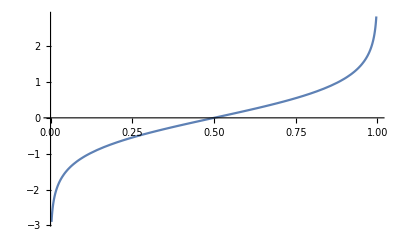

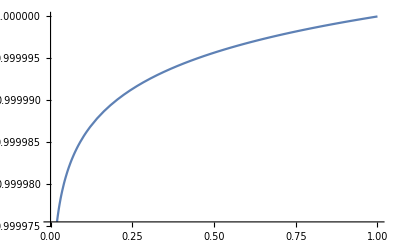

```mathematica
Plot[ϕos2/.m->0.01/l,{y,0,1}]
Plot[ϕos1/.m->0.01/l,{y,0,1}]
```

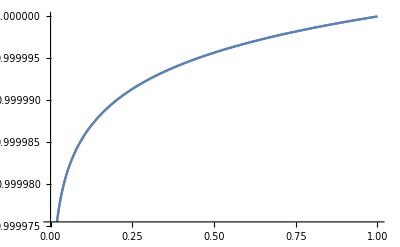

```mathematica
Show[{Plot[ϕos1/.m->0.01/l,{y,0,1}], Plot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,1-y]/.m->0.01/l,{y,0,1}] }]
```

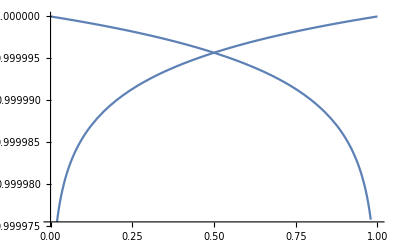

```mathematica
Show[{Plot[ϕos1/.m->0.01/l,{y,0,1}], Plot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,y]/.m->0.01/l,{y,0,1}] }]
```

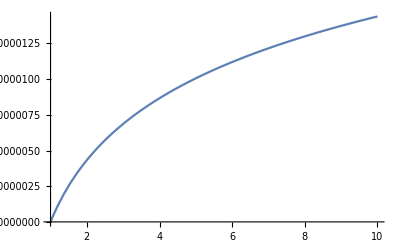

```mathematica
Show[{Plot[ϕos1/.m->0.01/l,{y,1,10}], Plot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,y]/.m->0.01/l,{y,1,10}] }]
```

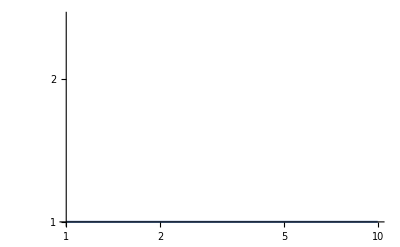

```mathematica
Show[{LogLogPlot[ϕos2/.m->0.01/l,{y,1,10}], LogLogPlot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,1-y]/.m->0.01/l,{y,1,10}] }]
```

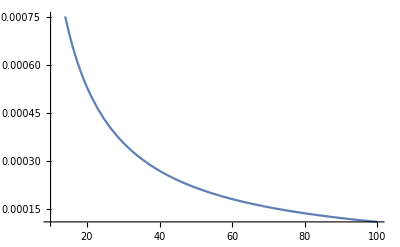

```mathematica
ϕCR[ρ_,ϵ_]:=(ρ^ϵ-ϵ/8 ρ^(-4+ϵ)+ϵ/8 ρ^(-4-ϵ))
Plot[ϕCR[ρ,0.01]D[ϕCR[ρ,0.01],ρ]/.ρ->a,{a,10,100}]
```

This shows that the solution we got in Mathematica matches CR - to be more explicit: so at least the second works.

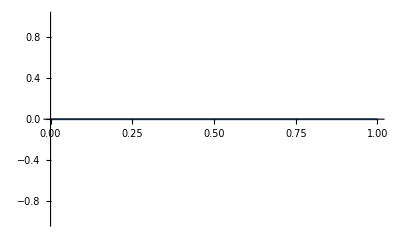

```mathematica
Show[{Plot[(ϕos1 -Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,1-y])/.m->0.01/l,{y,0,1}] }]
```

It looks like the other solution they give is just a flipped version of the same thing.

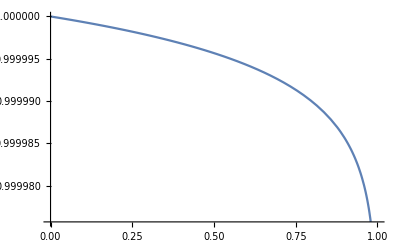

```mathematica
Plot[(Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,y])/.m->0.01/l,{y,0,1}]
```

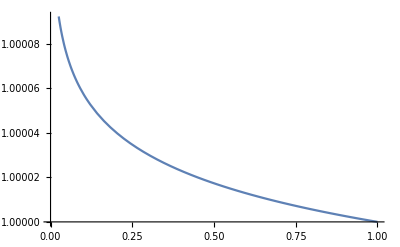

```mathematica
Plot[ϕos1/.{m->0.01/l,y->ρ^4}/.ρ->1/z,{z,0,1}]
```

#### Put ϕ on it’s EOM

```mathematica
Simplify[Sqrt[g5y](Inverse[gy][[3,3]] D[ϕos1,y]^2 - m^2  ϕos1^2)]
```

1/4 (-m^2 LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+2 y]^2+1/(4 l^2 (-1+y) y)(2+√(4+l^2 m^2))^2 ((1-2 y) LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+2 y]+LegendreP[1/4 (2+√(4+l^2 m^2)),-1+2 y])^2) √((r^4 ρh^8 Sin[θ]^2)/l^6)

```mathematica
Simplify[Sqrt[g5y](Inverse[gy][[3,3]] D[ϕ[y],y]^2 - m^2  ϕ[y]^2)]
Simplify[Sqrt[g5y](1/2-1/Sqrt[g5y] D[Sqrt[g5y]Inverse[gy][[3,3]]D[ϕ[y],y] ,y]+ m^2  ϕ[y]^2)]
```

1/4 √((r^4 ρh^8 Sin[θ]^2)/l^6) (-m^2 ϕ[y]^2+(16 (-1+y) y ϕ'[y]^2)/l^2)

(√((r^4 ρh^8 Sin[θ]^2)/l^6) (l^2 m^2 ϕ[y]^2+(8-16 y) ϕ'[y]-8 (-1+y) y ϕ''[y]))/(4 l^2)

Could this be a mistake in CR? 

this is supposed to vanish on shell, but there is a square here, which I don’t understand.

```mathematica
D[LegendreP[a,b],b]
```

((-1-a) b LegendreP[a,b]+(1+a) LegendreP[1+a,b])/(-1+b^2)

```mathematica
ϕos1z =ϕos1/.y->ρ^4/ρh^4/.{ρ->l^2/z,ρh->l^2/zh};
Simplify[Sqrt[Det[met5D]](met5D[[3,3]] D[ϕos1z,z]^2 - m^2  ϕos1z^2)]
```

(-m^2 LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+(2 zh^4)/z^4]^2+(l^2 (2+√(4+l^2 m^2))^2 ((z^4-2 zh^4) LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+(2 zh^4)/z^4]+z^4 LegendreP[1/4 (2+√(4+l^2 m^2)),-1+(2 zh^4)/z^4])^2)/(4 z^4 (z^4-zh^4)^2 g[z])) √((l^10 r^4 Sin[θ]^2)/z^10)

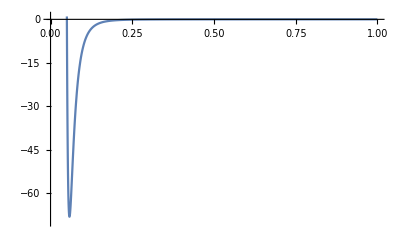

```mathematica
Plot[(Simplify[l^5/z^5(met5D[[3,3]] D[ϕos1z,z]^2 - m^2  ϕos1z^2)]/.{m->0.01/l,g[z]->1-z^4/zh^4}/.{zh->1,l->1})/.z->a,{a,0,1},PlotRange->{-70,1}]
```

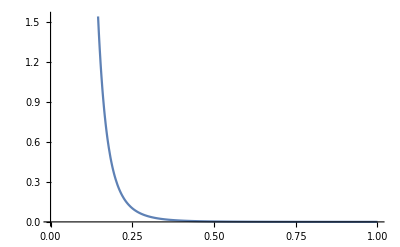

```mathematica
Plot[(Simplify[l^5/z^5(Inverse[met5D][[3,3]] D[ϕos1z,z]^2 + m^2  ϕos1z^2)]/.{m->0.01/l,g[z]->1-z^4/zh^4}/.{zh->1,l->1})/.z->a,{a,0,1}]
```

```mathematica
NIntegrate[(Simplify[l^5/z^5(met5D[[3,3]] D[ϕos1z,z]^2 - m^2  ϕos1z^2)]/.{m->0.01/l,g[z]->1-z^4/zh^4}/.{zh->1,l->1})/.z->a,{a,0.05,1}]
NIntegrate[(Simplify[l^5/z^5(met5D[[3,3]] D[ϕos1z,z]^2 - m^2  ϕos1z^2)]/.{m->0.01/l,g[z]->1-z^4/zh^4}/.{zh->1,l->1})/.z->a,{a,0.05,0.9}]
NIntegrate[(Simplify[l^5/z^5(met5D[[3,3]] D[ϕos1z,z]^2 - m^2  ϕos1z^2)]/.{m->0.01/l,g[z]->1-z^4/zh^4}/.{zh->1,l->1})/.z->a,{a,0.05,0.8}]
NIntegrate[(Simplify[l^5/z^5(met5D[[3,3]] D[ϕos1z,z]^2 - m^2  ϕos1z^2)]/.{m->0.01/l,g[z]->1-z^4/zh^4}/.{zh->1,l->1})/.z->a,{a,0.05,0.2}]
NIntegrate[(Simplify[l^5/z^5(met5D[[3,3]] D[ϕos1z,z]^2 - m^2  ϕos1z^2)]/.{m->0.01/l,g[z]->1-z^4/zh^4}/.{zh->1,l->1})/.z->a,{a,0.05,0.1}]
NIntegrate[(Simplify[l^5/z^5(met5D[[3,3]] D[ϕos1z,z]^2 - m^2  ϕos1z^2)]/.{m->0.01/l,g[z]->1-z^4/zh^4}/.{zh->1,l->1})/.z->a,{a,0.05,0.06}]
```

-2.00024

-2.00022

-2.0002

-1.98467

-1.75805

-0.536207

This is our potential from the bulk scalar, so we must also include the boundary term from the planck brane

and I think we will need to give neumann bcs to the scalar on the probe brane, or we will need to figure out how to consistently give dynamics.

Seems feasible since CR need this in order to couple the GW scalar to the radion on the RS side.

Also I think this will have the opposite sign in our action.

#### Horizon regularity

```mathematica
gtilde= r^2/z^4{{g[z],0,0},{0,1,0},{0,0,1/g[z]}}
X= {t[ζ],r[ζ],z[ζ],θ,ϕ};
x= {ζ};
JXx=Table[D[X[[i]],x[[j]]],{i,3},{j,1}];
s = Simplify[Transpose[JXx].(gtilde/.g[z]->1-z^4/zh^4/.{z->z[ζ],r->r[ζ]}).JXx ];
s //MatrixForm 
Det[s]
```

{{(r^2 g[z])/z^4,0,0},{0,r^2/z^4,0},{0,0,r^2/(z^4 g[z])}}

((r[ζ]^2 (r'[ζ]^2+(1-z[ζ]^4/zh^4) t'[ζ]^2+z'[ζ]^2/(1-z[ζ]^4/zh^4)))/z[ζ]^4)

(r[ζ]^2 (r'[ζ]^2+(1-z[ζ]^4/zh^4) t'[ζ]^2+z'[ζ]^2/(1-z[ζ]^4/zh^4)))/z[ζ]^4

```mathematica
Simplify[D[ζ D[s,r'[ζ]][[1,1]],ζ]]
Simplify[Solve[%==0,r''[ζ]]]
```

(2 r[ζ] (2 ζ z[ζ] r'[ζ]^2+r[ζ] (-4 ζ r'[ζ] z'[ζ]+z[ζ] (r'[ζ]+ζ r''[ζ]))))/z[ζ]^5

{{r''[ζ]→r'[ζ] (-1/ζ-(2 r'[ζ])/r[ζ]+(4 z'[ζ])/z[ζ])}}

Try with y variable

```mathematica
gtilde = (r^2 l^2)/z^4{{g[z],0,0},{0,1,0},{0,0,1/g[z]}}
X= {t,r,l^2/ρ};
x= {t,r,ρ};
JXx=Table[D[X[[i]],x[[j]]],{i,3},{j,3}];
gρ = Simplify[Transpose[JXx].(gtilde/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ];
gρ //MatrixForm 
Simplify[Det[gρ]]

X= {t,r,ρh y^(1/4)};
x= {t,r,y};
JXx=Table[D[X[[i]],x[[j]]],{i,3},{j,3}];
gytilde = Simplify[Transpose[JXx].(gρ/.ρ->ρh y^(1/4)).JXx ]
gytilde //MatrixForm 
Simplify[Det[gytilde]]
```

{{(l^2 r^2 g[z])/z^4,0,0},{0,(l^2 r^2)/z^4,0},{0,0,(l^2 r^2)/(z^4 g[z])}}

((r^2 (ρ^4-ρh^4))/l^6 | 0 | 0
0 | (r^2 ρ^4)/l^6 | 0
0 | 0 | r^2/(l^2 (1-ρh^4/ρ^4)))

(r^6 ρ^8)/l^14

{{(r^2 (-1+y) ρh^4)/l^6,0,0},{0,(r^2 y ρh^4)/l^6,0},{0,0,(r^2 ρh^2)/(16 l^2 (-1+y) √y)}}

((r^2 (-1+y) ρh^4)/l^6 | 0 | 0
0 | (r^2 y ρh^4)/l^6 | 0
0 | 0 | (r^2 ρh^2)/(16 l^2 (-1+y) √y))

(r^6 √y ρh^10)/(16 l^14)

```mathematica
Print["convert to z dependent metric"]
X= {t[ζ],r[ζ],y[ζ]};
x= {ζ};
JXx=Table[D[X[[i]],x[[j]]],{i,3},{j,1}];
gyζ = Simplify[Transpose[JXx].(gytilde/.y->y[ζ]).JXx ];
gyζ //MatrixForm 

Print["find y eom"]

yeom1 =Simplify[D[ζ D[gyζ,y'[ζ]][[1,1]],ζ]]
yeom = y''[ζ]+(y''[ζ]/.Simplify[Solve[yeom1==0,y''[ζ]]][[1,1]])

Print["find regularity condition at the horizon (y=1)"]
Solve[Numerator[yeom-y''[ζ]]==0,y'[ζ]]
%/.y[ζ]->1

Print["find eom at the horizon"]
yeom/.{y'[ζ]->0}
Simplify[yeom1/.y'[ζ]->0]
```

convert to z dependent metric

((r^2 ρh^2 (16 ρh^2 y[ζ] r'[ζ]^2+16 ρh^2 (-1+y[ζ]) t'[ζ]^2+(l^4 y'[ζ]^2)/((-1+y[ζ]) √y[ζ])))/(16 l^6))

find y eom

(r^2 ρh^2 (ζ y'[ζ]^2+2 y[ζ]^2 (y'[ζ]+ζ y''[ζ])-y[ζ] (2 y'[ζ]+3 ζ y'[ζ]^2+2 ζ y''[ζ])))/(16 l^2 (-1+y[ζ])^2 y[ζ]^(3/2))

(y'[ζ] (-2 y[ζ]^2-ζ y'[ζ]+y[ζ] (2+3 ζ y'[ζ])))/(2 ζ (-1+y[ζ]) y[ζ])+y''[ζ]

find regularity condition at the horizon (y=1)

{{y'[ζ]→0},{y'[ζ]→(2 (-y[ζ]+y[ζ]^2))/(ζ (-1+3 y[ζ]))}}

{{y'[ζ]→0},{y'[ζ]→0}}

find eom at the horizon

y''[ζ]

(r^2 ζ ρh^2 y''[ζ])/(8 l^2 (-1+y[ζ]) √y[ζ])

So it looks like we need y’[ζ]=0 and y’’[ζ] at the horizon. Which in terms of z gives.

```mathematica
y/.y->(ρ/ρh)^4/.{ρ->l^2/z,ρh->l^2/zh}
y'==D[%/.z->z[ζ],{ζ,1}] 
D[%%/.z->z[ζ],{ζ,2}] /.z'[ζ]->0
```

zh^4/z^4

y'==-(4 zh^4 z'[ζ])/z[ζ]^5

-(4 zh^4 z''[ζ])/z[ζ]^5

So z’’ and z’ must both vanish at the horizon. 

AT LEAST IN THE ABSENCE OF A POTENTIAL. ONCE THESE ARE ADDED IN THEY CAN AUGMENT THESE CONDITIONS

#### Right to y from z in cartesian

```mathematica
gzE=l^2/z^2{{g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
X= {t,zh/y^(1/4),x1,x2,x3};
x= {t,y,x1,x2,x3};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gy = Simplify[Transpose[JXx].(gzE/.g[z]->1-z^4/zh^4/.z->zh/y^(1/4)).JXx ];
gy //MatrixForm 
g5y = Simplify[Det[gy]]

ϕeqn =Simplify[-(1/(√g5y)D[√g5y Inverse[gy][[2,2]]D[ϕ[y],y],y]-m^2 ϕ[y])l^2]==0
(*Simplify[ϕeqn/.ρ->y/ρh/.ϕ[ρh-ρ]->ϕ[ρ]]*)
ϕsol=DSolve[ϕeqn,ϕ[y],y];
(*ϕsol=DSolve[ϕeqn,ϕ[1/ρ],ρ];*)
ϕos1=ϕ[y]/.ϕsol[[1]]/.{C[1]->1,C[2]->0}
ϕos2=ϕ[y]/.ϕsol[[1]]/.{C[1]->0,C[2]->1}
```

((l^2 (-1+y))/(√y zh^2) | 0 | 0 | 0 | 0
0 | l^2/(16 (-1+y) y) | 0 | 0 | 0
0 | 0 | (l^2 √y)/zh^2 | 0 | 0
0 | 0 | 0 | (l^2 √y)/zh^2 | 0
0 | 0 | 0 | 0 | (l^2 √y)/zh^2)

l^10/(16 zh^8)

l^2 m^2 ϕ[y]-16 ((-1+2 y) ϕ'[y]+(-1+y) y ϕ''[y])==0

LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

LegendreQ[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

```mathematica
ϕos1type3 = LegendreP[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]
ϕos2type3 =LegendreQ[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]
```

LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

LegendreQ[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]

```mathematica
Simplify[gy zh^2/(l^2 √y)]
```

{{(-1+y)/y,0,0,0,0},{0,zh^2/(16 (-1+y) y^(3/2)),0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

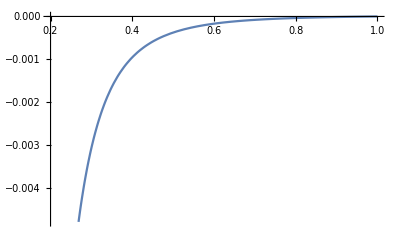

```mathematica
Plot[-(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.01/l/.l->2/.y->1/a^4),{a,0.2,1}]
```

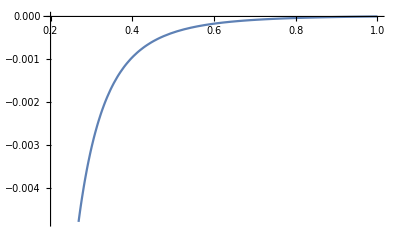

```mathematica
Plot[-(Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.01/l/.l->2/.y->1/a^4),{a,0.2,1}]
```

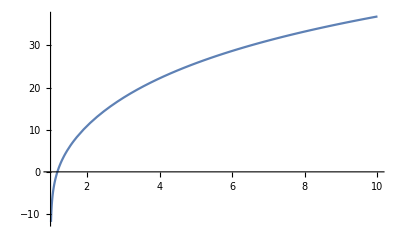

```mathematica
Plot[(ϕos2 Inverse[gy][[2,2]]D[ϕos2,y]/.m->0.1/l/.l->1)/.y->1/a^4,{a,1,10}]
```

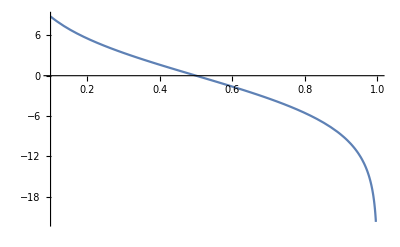

```mathematica
Plot[(ϕos2 Inverse[gy][[2,2]]D[ϕos2,y]/.m->0.1/l/.l->1)/.y->a,{a,0.1,1}]
```

```mathematica
ϕos2
```

LegendreQ[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

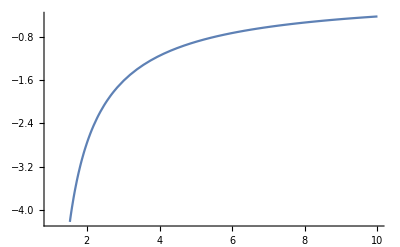

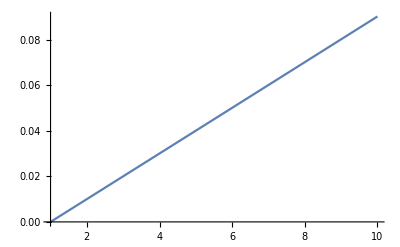

```mathematica
Plot[(ϕos2type3 Inverse[gy][[2,2]]D[ϕos2type3,y]/.m->0.1/l/.l->1)/.y->a,{a,1,10}]
Plot[(ϕos1type3 Inverse[gy][[2,2]]D[ϕos1type3,y]/.m->0.1/l/.l->1)/.y->a,{a,1,10}]
```

```mathematica
Plot[(ϕos2type3/.m->0.1/l/.l->1)/.y->a,{a,0,1}]
```

-Graphics-

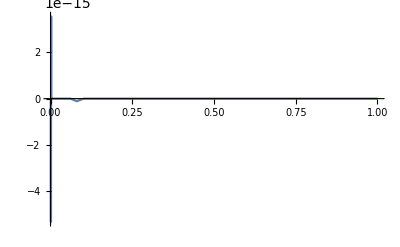

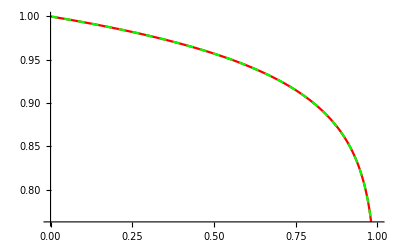

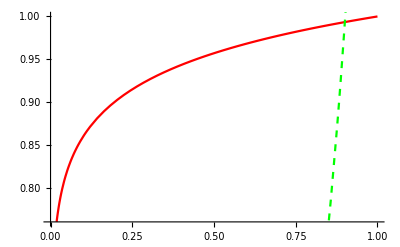

```mathematica
Plot[(ϕos1-Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,1-y])/.m->1/l,{y,0,1}]
Show[{Plot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,y]/.m->1/l,{y,0,1},PlotStyle->Red],Plot[ϕos1/.m->1/l/.y->1-a,{a,0,1},PlotStyle->{Green,Dashed}]}]
Show[{Plot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,1-y]/.m->1/l,{y,0,1},PlotStyle->Red],Plot[ϕos2/.m->1/l,{y,0,1},PlotStyle->{Green,Dashed}]}]
```

```mathematica
Solve[b^2-b-m^2 l^2/16==0,b]
```

{{b→1/4 (2-√(4+l^2 m^2))},{b→1/4 (2+√(4+l^2 m^2))}}

Add the radion potetntial from section 1?

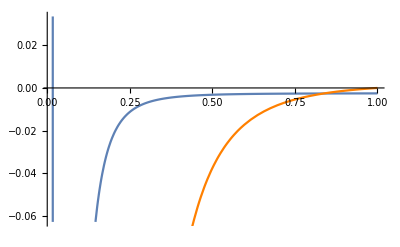

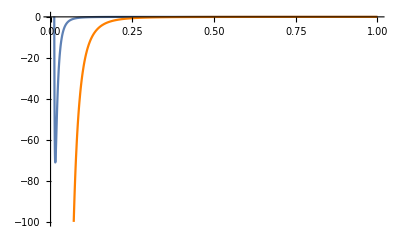

```mathematica
Show[{Plot[-2.55 10^-3 a^-4+(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0.01,1}],Plot[-(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0.01,1},PlotStyle->Orange]}]
Show[{Plot[-2.555 10^-3 a^-4+(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1},PlotRange->{-100,0.2}],Plot[-(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1},PlotStyle->Orange,PlotRange->{-100,0.2}]}]
```

Should be a^4 not a^-4, also wrong sign on the GW potential

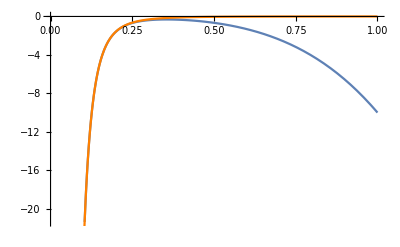

```mathematica
Show[{Plot[- 10^1 a^4-(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1}],Plot[-(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1},PlotStyle->Orange,PlotRange->{-100,0.2}]}]
```

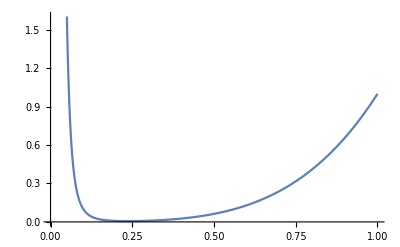

```mathematica
Plot[((1/a)^(-2 -√(4 +m^2 l^2))+10^-5(1/a)^(2 +√(4 +m^2 l^2)))/.m->0.1/l,{a,0,1}]
```

Maybe I have the sign wrong above? This looks like minus the potential we have above. 

Should check signs carefully.

could also be Euclidean time, there’s the whole minus potential thing in coleman.

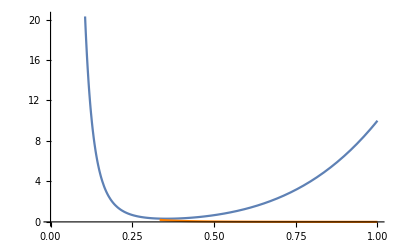

```mathematica
Show[{Plot[ 10^1 a^4+(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1}],Plot[(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1},PlotStyle->Orange,PlotRange->{-100,0.2}]}]
```

I would expect so given that close to UV brane, we are essentially in AdS and so it should match on to the RS GW solution to a good approximation . But the radion will probably still pull it towards the BB

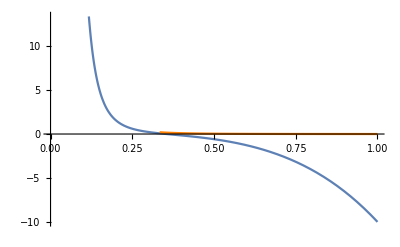

```mathematica
Show[{Plot[ -10^1 a^4+(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1}],Plot[(ϕos1 Inverse[gy][[2,2]]D[ϕos1,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1},PlotStyle->Orange,PlotRange->{-100,0.2}]}]
```

Note, the sign of the coefficient for ϕ is irrelevant to this discussion since it will be squared.

```mathematica
Show[{Plot[ ((ϕos1+ϕos2) Inverse[gy][[2,2]]D[ϕos1+ϕos2,y]/.m->0.1/l/.l->2/.y->1/a^4),{a,0,1}],}]
```

Show::gcomb: Could not combine the graphics objects in Show[{,Null}].

Show[{-Graphics-,Null}]

#### Fix with branch cuts

```mathematica
Plot[(ϕos2type3 Inverse[gy][[2,2]]D[ϕos2type3,y]/.m->0.1/l/.l->1)/.y->a,{a,1,10}]
Plot[(ϕos1type3 Inverse[gy][[2,2]]D[ϕos1type3,y]/.m->0.1/l/.l->1)/.y->a,{a,1,10}]
```

-Graphics-

-Graphics-

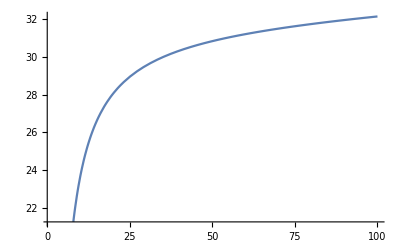

```mathematica
Plot[((-5ϕos2type3 +ϕos1type3)Inverse[gy][[2,2]]D[-4ϕos2type3+ ϕos1type3,y]/.m->0.1/l/.l->1)/.y->a,{a,1,100}]
```

```mathematica
NSolve[(D[(A ϕos2type3 +B ϕos1type3)Inverse[gy][[2,2]]D[A ϕos2type3+ B ϕos1type3,y],y]/.m->0.1/l/.l->1/.y->a)==0]
```

$Aborted